```mathematica
ClearAll["Global`*"]
```

```mathematica
Residue[ DDa2[9,x],{x,0}]
```

1

```mathematica
Limit[DDa2[100,z] - 1/z,{z->0}]
```

{428/15}

```mathematica
Expand[DDa[9,x]/x]
```

16/3+1/x+(5 x)/2+x^2/6

```mathematica
16/3+1/x+(5 x)/2+x^2/6
```

```mathematica
f2[x_] := 16/3+1/x+(5 x)/2+x^2/6
```

```mathematica
f2[3]
```

44/3

```mathematica
DDa2[9,3]
```

44/3

```mathematica
K[n_]:=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
P[n_,k_]:=P[n,k]=Sum[ K[j]P[Floor[n/j],k-1],{j,2,n}];P[n_,0]:=1
D2[n_,k_]:=D2[n,k]=Sum[D2[Floor[n/j],k-1],{j,2,n}];D2[n_,0]:=1
DD[n_,z_]:=Sum[FactorialPower[z,a]/a! D2[n,a],{a,0,Log[2,n]}]
P[n_,k_,s_]:=P[n,k,s]=Sum[ j^-s K[j]P[Floor[n/j],k-1,s],{j,2,n}];P[n_,0,s_]:=1
DDa[n_, z_] := Sum[ z^k/k! P[n,k],{k,0,Log[2,n]}]
DDa[n_, z_,s_] := Sum[ z^k/k! P[n,k,s],{k,0,Log[2,n]}]
DDa2[n_, z_] := Sum[ z^k/k! P[n,k]/z,{k,0,Log[2,n]}]
Dhyp[n_,k_,a_]:=Dhyp[n,k,a]=Sum[Binomial[k,j] Dhyp[Floor[n/(m^(k-j))],j,m+1],{m,a,n^(1/k)},{j,0,k-1}]
Dhyp[n_,1,a_]:=Floor[n]-a+1;Dhyp[n_,0,a_]:=1
bins[ z_, a_] := Product[ (z-k),{k,0,a-1}]/a!
DDD[n_,z_]:=Expand[Sum[bins[z,a] Dhyp[n,a,2],{a,0,Log[2,n]}]]
lin[n_] := Sum[ (-1)^(k+1)/k Dhyp[n,k,2],{k,1,Log[2,n]}]
```

```mathematica
Roots[ 1+(9 x)/2+(3 x^2)/2==0,x]
```

x==1/6 (-9-√57)||x==1/6 (-9+√57)

```mathematica
FullSimplify[(-7/2+(√41)/2)-(-5/2+(√17)/2)]
```

```mathematica
Table[{n,Expand[Roots[ Expand[DDa[n,x]]==0,x]]},{n,2,16}]//TableForm
```

2 | x==-1
3 | x==-1/2
4 | x==-5/2-(√17)/2||x==-5/2+(√17)/2
5 | x==-7/2-(√41)/2||x==-7/2+(√41)/2
6 | x==-1/3||x==-2
7 | x==-3/2-(√(19/3))/2||x==-3/2+(√(19/3))/2
8 | x==-9/2-(√73)/2||x==-9/2+(√73)/2||x==-3
9 | x==-5+43/(3^(1/3) (-432+ⅈ √51897)^(1/3))+(-432+ⅈ √51897)^(1/3)/3^(2/3)||x==-5-43/(2 3^(1/3) (-432+ⅈ √51897)^(1/3))+(43 ⅈ 3^(1/6))/(2 (-432+ⅈ √51897)^(1/3))-(-432+ⅈ √51897)^(1/3)/(2 3^(2/3))-(ⅈ (-432+ⅈ √51897)^(1/3))/(2 3^(1/6))||x==-5-43/(2 3^(1/3) (-432+ⅈ √51897)^(1/3))-(43 ⅈ 3^(1/6))/(2 (-432+ⅈ √51897)^(1/3))-(-432+ⅈ √51897)^(1/3)/(2 3^(2/3))+(ⅈ (-432+ⅈ √51897)^(1/3))/(2 3^(1/6))
10 | x==-7+115/(3^(1/3) (-2106+ⅈ √127389)^(1/3))+(-2106+ⅈ √127389)^(1/3)/3^(2/3)||x==-7-115/(2 3^(1/3) (-2106+ⅈ √127389)^(1/3))+(115 ⅈ 3^(1/6))/(2 (-2106+ⅈ √127389)^(1/3))-(-2106+ⅈ √127389)^(1/3)/(2 3^(2/3))-(ⅈ (-2106+ⅈ √127389)^(1/3))/(2 3^(1/6))||x==-7-115/(2 3^(1/3) (-2106+ⅈ √127389)^(1/3))-(115 ⅈ 3^(1/6))/(2 (-2106+ⅈ √127389)^(1/3))-(-2106+ⅈ √127389)^(1/3)/(2 3^(2/3))+(ⅈ (-2106+ⅈ √127389)^(1/3))/(2 3^(1/6))
11 | x==-7+109/(3^(1/3) (-1917+ⅈ √210198)^(1/3))+(-1917+ⅈ √210198)^(1/3)/3^(2/3)||x==-7-109/(2 3^(1/3) (-1917+ⅈ √210198)^(1/3))+(109 ⅈ 3^(1/6))/(2 (-1917+ⅈ √210198)^(1/3))-(-1917+ⅈ √210198)^(1/3)/(2 3^(2/3))-(ⅈ (-1917+ⅈ √210198)^(1/3))/(2 3^(1/6))||x==-7-109/(2 3^(1/3) (-1917+ⅈ √210198)^(1/3))-(109 ⅈ 3^(1/6))/(2 (-1917+ⅈ √210198)^(1/3))-(-1917+ⅈ √210198)^(1/3)/(2 3^(2/3))+(ⅈ (-1917+ⅈ √210198)^(1/3))/(2 3^(1/6))
12 | x==-3/2-(√7)/2||x==-3/2+(√7)/2||x==-3
13 | x==-2+1/6 (486-6 √6513)^(1/3)+(81+√6513)^(1/3)/6^(2/3)||x==-2-1/12 (486-6 √6513)^(1/3)-(ⅈ (486-6 √6513)^(1/3))/(4 √3)+(ⅈ (81+√6513)^(1/3))/(2 2^(2/3) 3^(1/6))-(81+√6513)^(1/3)/(2 6^(2/3))||x==-2-1/12 (486-6 √6513)^(1/3)+(ⅈ (486-6 √6513)^(1/3))/(4 √3)-(ⅈ (81+√6513)^(1/3))/(2 2^(2/3) 3^(1/6))-(81+√6513)^(1/3)/(2 6^(2/3))
14 | x==-5/2+31/(2 3^(1/3) (-189+2 ⅈ √13413)^(1/3))+(-189+2 ⅈ √13413)^(1/3)/(2 3^(2/3))||x==-5/2-31/(4 3^(1/3) (-189+2 ⅈ √13413)^(1/3))+(31 ⅈ 3^(1/6))/(4 (-189+2 ⅈ √13413)^(1/3))-(-189+2 ⅈ √13413)^(1/3)/(4 3^(2/3))-(ⅈ (-189+2 ⅈ √13413)^(1/3))/(4 3^(1/6))||x==-5/2-31/(4 3^(1/3) (-189+2 ⅈ √13413)^(1/3))-(31 ⅈ 3^(1/6))/(4 (-189+2 ⅈ √13413)^(1/3))-(-189+2 ⅈ √13413)^(1/3)/(4 3^(2/3))+(ⅈ (-189+2 ⅈ √13413)^(1/3))/(4 3^(1/6))
15 | x==-3+(-405+ⅈ √32583)^(1/3)/6^(2/3)+(16 2^(2/3))/(3 (-405+ⅈ √32583))^(1/3)||x==-3+(8 ⅈ 2^(2/3) 3^(1/6))/(-405+ⅈ √32583)^(1/3)-(ⅈ (-405+ⅈ √32583)^(1/3))/(2 2^(2/3) 3^(1/6))-(-405+ⅈ √32583)^(1/3)/(2 6^(2/3))-(8 2^(2/3))/(3 (-405+ⅈ √32583))^(1/3)||x==-3-(8 ⅈ 2^(2/3) 3^(1/6))/(-405+ⅈ √32583)^(1/3)+(ⅈ (-405+ⅈ √32583)^(1/3))/(2 2^(2/3) 3^(1/6))-(-405+ⅈ √32583)^(1/3)/(2 6^(2/3))-(8 2^(2/3))/(3 (-405+ⅈ √32583))^(1/3)
16 | x==-11/2-53/(2 √(3 (53+(1401155-18 √314550701)^(1/3)+(1401155+18 √314550701)^(1/3))))-(1401155-18 √314550701)^(1/3)/(2 √(3 (53+(1401155-18 √314550701)^(1/3)+(1401155+18 √314550701)^(1/3))))-(1401155+18 √314550701)^(1/3)/(2 √(3 (53+(1401155-18 √314550701)^(1/3)+(1401155+18 √314550701)^(1/3))))-1/2 √(106/3-1/3 (1401155-18 √314550701)^(1/3)-1/3 (1401155+18 √314550701)^(1/3)-384 √(3/(53+(1401155-18 √314550701)^(1/3)+(1401155+18 √314550701)^(1/3))))||x==-11/2-53/(2 √(3 (53+(1401155-18 √314550701)^(1/3)+(1401155+18 √314550701)^(1/3))))-(1401155-18 √314550701)^(1/3)/(2 √(3 (53+(1401155-18 √314550701)^(1/3)+(1401155+18 √314550701)^(1/3))))-(1401155+18 √314550701)^(1/3)/(2 √(3 (53+(1401155-18 √314550701)^(1/3)+(1401155+18 √314550701)^(1/3))))+1/2 √(106/3-1/3 (1401155-18 √314550701)^(1/3)-1/3 (1401155+18 √314550701)^(1/3)-384 √(3/(53+(1401155-18 √314550701)^(1/3)+(1401155+18 √314550701)^(1/3))))||x==-11/2+53/(2 √(3 (53+(1401155-18 √314550701)^(1/3)+(1401155+18 √314550701)^(1/3))))+(1401155-18 √314550701)^(1/3)/(2 √(3 (53+(1401155-18 √314550701)^(1/3)+(1401155+18 √314550701)^(1/3))))+(1401155+18 √314550701)^(1/3)/(2 √(3 (53+(1401155-18 √314550701)^(1/3)+(1401155+18 √314550701)^(1/3))))-1/2 √(106/3-1/3 (1401155-18 √314550701)^(1/3)-1/3 (1401155+18 √314550701)^(1/3)+384 √(3/(53+(1401155-18 √314550701)^(1/3)+(1401155+18 √314550701)^(1/3))))||x==-11/2+53/(2 √(3 (53+(1401155-18 √314550701)^(1/3)+(1401155+18 √314550701)^(1/3))))+(1401155-18 √314550701)^(1/3)/(2 √(3 (53+(1401155-18 √314550701)^(1/3)+(1401155+18 √314550701)^(1/3))))+(1401155+18 √314550701)^(1/3)/(2 √(3 (53+(1401155-18 √314550701)^(1/3)+(1401155+18 √314550701)^(1/3))))+1/2 √(106/3-1/3 (1401155-18 √314550701)^(1/3)-1/3 (1401155+18 √314550701)^(1/3)+384 √(3/(53+(1401155-18 √314550701)^(1/3)+(1401155+18 √314550701)^(1/3))))

```mathematica
DD[12, -3]
```

0

```mathematica
Table[{n,N[Expand[Roots[ Expand[DDa[n,x]]==0,x]]]},{n,2,32}]//TableForm
```

2 | x==-1.
3 | x==-0.5
4 | x==-4.56155||x==-0.438447
5 | x==-6.70156||x==-0.298438
6 | x==-0.333333||x==-2.
7 | x==-2.75831||x==-0.241694
8 | x==-8.772||x==-0.227998||x==-3.
9 | x==-0.207381-1.33227×10^-15 ⅈ||x==-2.31959+1.77636×10^-15 ⅈ||x==-12.473-2.22045×10^-16 ⅈ
10 | x==-0.218507+2.66454×10^-15 ⅈ||x==-1.41809-1.77636×10^-15 ⅈ||x==-19.3634+0. ⅈ
11 | x==-0.174602+0. ⅈ||x==-1.80686+1.77636×10^-15 ⅈ||x==-19.0185-1.33227×10^-15 ⅈ
12 | x==-2.82288||x==-0.177124||x==-3.
13 | x==-0.14802||x==-2.92599+1.25394 ⅈ||x==-2.92599-1.25394 ⅈ
14 | x==-0.151746+4.44089×10^-16 ⅈ||x==-1.773-2.22045×10^-16 ⅈ||x==-5.57525-2.22045×10^-16 ⅈ
15 | x==-0.155907-8.88178×10^-16 ⅈ||x==-1.27033+6.66134×10^-16 ⅈ||x==-7.57377+2.22045×10^-16 ⅈ
16 | x==-10.2913-4.44128 ⅈ||x==-10.2913+4.44128 ⅈ||x==-1.2665||x==-0.150831
17 | x==-10.1642-4.18445 ⅈ||x==-10.1642+4.18445 ⅈ||x==-1.54283||x==-0.128751
18 | x==-1.72599-6.34634×10^-16 ⅈ||x==-0.129805+4.78239×10^-16 ⅈ||x==-28.368-3.01529×10^-17 ⅈ||x==-3.77618+1.86548×10^-16 ⅈ
19 | x==-0.113483-2.66454×10^-15 ⅈ||x==-28.4047-4.44089×10^-16 ⅈ||x==-2.4818+3.55271×10^-15 ⅈ||x==-3.
20 | x==-2.01579-0.978644 ⅈ||x==-2.01579+0.978644 ⅈ||x==-41.8542||x==-0.114201
21 | x==-0.115891+0. ⅈ||x==-41.209+1.77636×10^-15 ⅈ||x==-1.67512-1.77636×10^-15 ⅈ||x==-3.
22 | x==-1.22037-9.42146×10^-16 ⅈ||x==-0.117694+6.68801×10^-16 ⅈ||x==-40.5402-9.65607×10^-18 ⅈ||x==-4.12173+2.83001×10^-16 ⅈ
23 | x==-1.47239-4.9035×10^-16 ⅈ||x==-0.10394+1.58688×10^-16 ⅈ||x==-40.557+8.48301×10^-18 ⅈ||x==-3.86667+3.2318×10^-16 ⅈ
24 | x==-5.00304-2.42184 ⅈ||x==-5.00304+2.42184 ⅈ||x==-1.48963||x==-0.104295
25 | x==-5.03548-2.91604 ⅈ||x==-5.03548+2.91604 ⅈ||x==-1.4299||x==-0.0991419
26 | x==-5.16558-3.78035 ⅈ||x==-5.16558+3.78035 ⅈ||x==-1.16859||x==-0.100246
27 | x==-5.56913-3.37906 ⅈ||x==-5.56913+3.37906 ⅈ||x==-1.16462||x==-0.0971295
28 | x==-1.1831-2.4326×10^-16 ⅈ||x==-0.097597+1.6585×10^-16 ⅈ||x==-8.79004-1.59755×10^-17 ⅈ||x==-4.72927+9.33854×10^-17 ⅈ
29 | x==-1.39219-1.17138×10^-16 ⅈ||x==-0.0880418+5.31228×10^-17 ⅈ||x==-8.93869+7.64789×10^-18 ⅈ||x==-4.38108+5.63674×10^-17 ⅈ
30 | x==-1.66598-0.772391 ⅈ||x==-1.66598+0.772391 ⅈ||x==-16.1801||x==-0.0879758
31 | x==-1.65844-0.969339 ⅈ||x==-1.65844+0.969339 ⅈ||x==-16.2028||x==-0.0802821
32 | x==-0.0791241||x==-15.809-12.8148 ⅈ||x==-15.809+12.8148 ⅈ||x==-1.65148-0.966781 ⅈ||x==-1.65148+0.966781 ⅈ

```mathematica
{-1/-0.08028210516043632,LogIntegral[31.]}
```

{12.4561,13.3152}

```mathematica
{-1/-0.10429530346233817,LogIntegral[24.]}
```

{9.58816,11.2003}

```mathematica
N[Expand[Roots[ Expand[DDa[100,x]]==0,x]]]
```

x==-0.933809||x==-0.0372047||x==-11.1997-12.3982 ⅈ||x==-11.1997+12.3982 ⅈ||x==-2.67195-1.86184 ⅈ||x==-2.67195+1.86184 ⅈ

```mathematica
(-0.9338092178222002)^-1+(-0.03720467504094746)^-1+(-11.199685576035792-12.398224487807216 ⅈ)^-1+(-11.199685576035792+12.398224487807216 ⅈ)^-1+(-2.6719503346754907-1.8618449055430246 ⅈ)^-1+(-2.6719503346754907+1.8618449055430246 ⅈ)^-1
```

-28.5333-1.38778×10^-17 ⅈ

```mathematica
DD[100,-0.03720467504094746]
```

```mathematica
9.56179579958416*^-15
```

```mathematica
N[Expand[Roots[ Expand[DDa[7,x]]==0,x]]]
```

x==-2.75831||x==-0.241694

```mathematica
ff[z_] := (z+2.7583057392117913)(z+0.24169426078820844)/(2.7583057392117913*0.24169426078820844)
```

```mathematica
ff[3]
```

28.

```mathematica
DD[7,3]
```

28

```mathematica
Expand[3/2(z+2.7583057392117913)(z+0.24169426078820844)]
```

1.+4.5 z+(3 z^2)/2

```mathematica
ff[0]
```

1.

```mathematica
List[N[Expand[Roots[ Expand[DDa[93,x]]==0,x]]]]
```

{x==-119.654||x==-15.028||x==-0.0385352||x==-2.63978-1.84996 ⅈ||x==-2.63978+1.84996 ⅈ||x==-1.}

```mathematica
Expand[(-9/2-(√73)/2)(-9/2+(√73)/2)(-3)]
```

-6

```mathematica
Expand[(-7/2-(√41)/2)(-7/2+(√41)/2)]
```

2

```mathematica
Limit[ ((z+2.7583057392117913)(z+0.24169426078820844)/(2.7583057392117913*0.24169426078820844)-1)/z,z->0]
```

4.5

```mathematica
Limit[ ((z+2.7583057392117913)(z+0.24169426078820844)/(2.7583057392117913*0.24169426078820844)/z-1/z),z->0]
```

4.5

```mathematica
Limit[ ((z+2.7583057392117913)(z+0.24169426078820844)/(2.7583057392117913*0.24169426078820844 z)-1/z),z->0]
```

4.5

```mathematica
Limit[ ((0.6666666666666667+3. z+z^2)/(2.7583057392117913*0.24169426078820844 z)-1/z),z->0]
```

4.5

```mathematica
Limit[ ((0.6666666666666667/z+3.+z)/(0.6666666666666667)-1/z),z->0]
```

4.5

```mathematica
Limit[ ((1/z+3./0.6666666666666667+z/0.6666666666666667)-1/z),z->0]
```

4.5

```mathematica
Limit[ ((3./0.6666666666666667+z/0.6666666666666667)),z->0]
```

4.5

```mathematica
Limit[ ((3./0.6666666666666667)),z->0]
```

4.5

```mathematica
Expand[FullSimplify[(z-(-3/2-(√(19/3))/2))(z-(-3/2+(√(19/3))/2))/(((-3/2-(√(19/3))/2))((-3/2+(√(19/3))/2)))]]
```

1+(9 z)/2+(3 z^2)/2

```mathematica
Limit[ ((1+(9 z)/2+(3 z^2)/2)-1)/z,z->0]
```

9/2

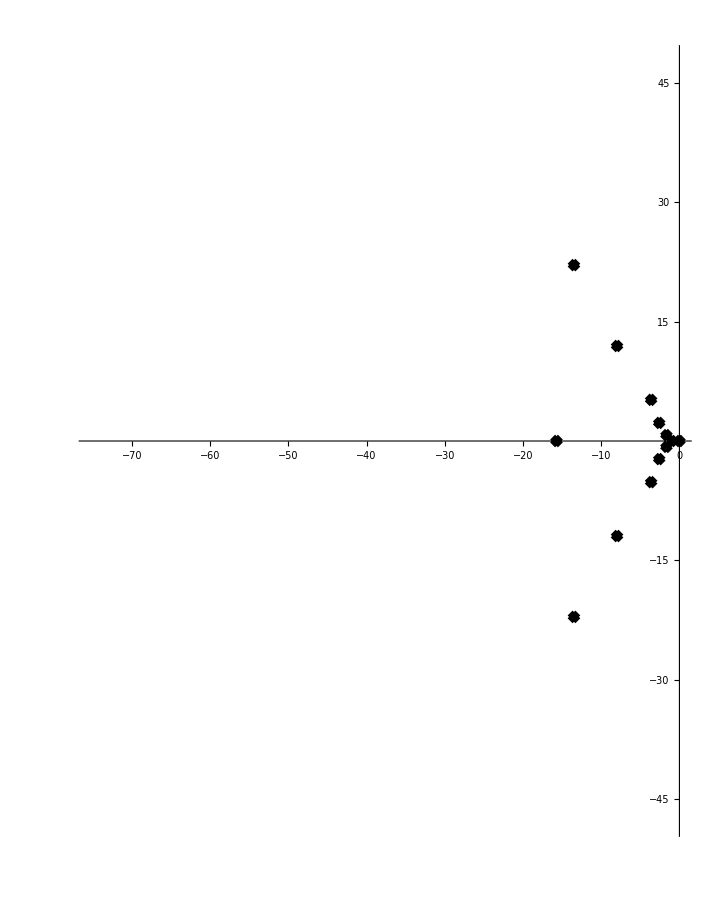

```mathematica
RootLocusPlot[1/Expand[DDa[117337,x]],{k,0,1},FeedbackType->None]
```

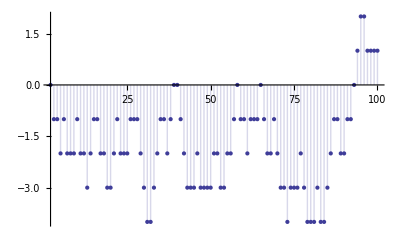

```mathematica
DiscretePlot[ DD[n,-1],{n,2,100}]
```

```mathematica
Table[{n,Expand[Roots[ Expand[DDa[n,x,s]]==0,x]]},{n,2,7}]//TableForm
```

2 | 2^s+x==0
3 | 6^s/(2^s+3^s)+x==0
4 | 1+2^(1+s)+2^(1+2 s) 3^-s+2 x==3^-s √(-2^(3+2 s) 9^s+(2^(1+2 s)+3^s (1+2^(1+s)))^2)||1+2^(1+s)+2^(1+2 s) 3^-s+3^-s √(-2^(3+2 s) 9^s+(2^(1+2 s)+3^s (1+2^(1+s)))^2)+2 x==0
5 | 15^-s √(-2^(3+2 s) 225^s+(2^(1+2 s) 3^s+5^s (2^(1+2 s)+3^s (1+2^(1+s))))^2)==1+2^(1+s)+2^(1+2 s) 3^-s+2^(1+2 s) 5^-s+2 x||15^-s (2^(1+s) 15^s+2^(1+2 s) (3^s+5^s)+√(-2^(3+2 s) 225^s+(2^(1+2 s) 3^s+5^s (2^(1+2 s)+3^s (1+2^(1+s))))^2)+15^s (1+2 x))==0
6 | x==-(5^-s (15^s+2^(1+s) 15^s+2^(1+2 s) (3^s+5^s)+√(-2^(3+2 s) 75^s (2^(1+s)+3^s)+(2^(1+2 s) 3^s+5^s (2^(1+2 s)+3^s (1+2^(1+s))))^2)))/(2 (2^(1+s)+3^s))||(5^-s (15^s+2^(1+s) 15^s+2^(1+2 s) (3^s+5^s)-√(-2^(3+2 s) 75^s (2^(1+s)+3^s)+(2^(1+2 s) 3^s+5^s (2^(1+2 s)+3^s (1+2^(1+s))))^2)))/(2 (2^(1+s)+3^s))+x==0
7 | (35^-s (2^(1+2 s) (15^s+21^s+35^s)+√(-2^(3+2 s) 3675^s (2^(1+s)+3^s)+(105^s (1+2^(1+s))+2^(1+2 s) (15^s+21^s+35^s))^2)+105^s (1+2 x)+2^(1+s) 35^s (3^s+2 x)))/(2^(1+s)+3^s)==0||(35^-s (105^s+2^(1+s) 105^s+2^(1+2 s) (15^s+21^s+35^s)-√(-2^(3+2 s) 3675^s (2^(1+s)+3^s)+(105^s (1+2^(1+s))+2^(1+2 s) (15^s+21^s+35^s))^2)))/(2 (2^(1+s)+3^s))+x==0

```mathematica
Table[{n,Expand[Roots[ Expand[DDa[n,x,s]]==0,x]]},{n,2,7}]//TableForm
```

2 | x==-2^s
3 | x==-6^s/(2^s+3^s)
4 | x==-1/2-2^s-2^(2 s) 3^-s-1/2 3^-s √(-2^(3+2 s) 3^(2 s)+(2^(1+2 s)+3^s+2^(1+s) 3^s)^2)||x==-1/2-2^s-2^(2 s) 3^-s+1/2 3^-s √(-2^(3+2 s) 3^(2 s)+(2^(1+2 s)+3^s+2^(1+s) 3^s)^2)
5 | x==-1/2-2^s-2^(2 s) 3^-s-2^(2 s) 5^-s-1/2 15^-s √(-2^(3+2 s) 15^(2 s)+(2^(1+2 s) 3^s+2^(1+2 s) 5^s+15^s+2^(1+s) 15^s)^2)||x==-1/2-2^s-2^(2 s) 3^-s-2^(2 s) 5^-s+1/2 15^-s √(-2^(3+2 s) 15^(2 s)+(2^(1+2 s) 3^s+2^(1+2 s) 5^s+15^s+2^(1+s) 15^s)^2)
6 | x==-(2^(2 s) 3^s)/(2^(1+s) 5^s+15^s)-(2^(2 s) 5^s)/(2^(1+s) 5^s+15^s)-15^s/(2 (2^(1+s) 5^s+15^s))-30^s/(2^(1+s) 5^s+15^s)-(√(-2^(3+2 s) 15^s (2^(1+s) 5^s+15^s)+(2^(1+2 s) 3^s+2^(1+2 s) 5^s+15^s+2^(1+s) 15^s)^2))/(2 (2^(1+s) 5^s+15^s))||x==-(2^(2 s) 3^s)/(2^(1+s) 5^s+15^s)-(2^(2 s) 5^s)/(2^(1+s) 5^s+15^s)-15^s/(2 (2^(1+s) 5^s+15^s))-30^s/(2^(1+s) 5^s+15^s)+(√(-2^(3+2 s) 15^s (2^(1+s) 5^s+15^s)+(2^(1+2 s) 3^s+2^(1+2 s) 5^s+15^s+2^(1+s) 15^s)^2))/(2 (2^(1+s) 5^s+15^s))
7 | x==-(2^(2 s) 15^s)/(2^(1+s) 35^s+105^s)-(2^(2 s) 21^s)/(2^(1+s) 35^s+105^s)-(2^(2 s) 35^s)/(2^(1+s) 35^s+105^s)-105^s/(2 (2^(1+s) 35^s+105^s))-210^s/(2^(1+s) 35^s+105^s)-(√(-2^(3+2 s) 105^s (2^(1+s) 35^s+105^s)+(2^(1+2 s) 15^s+2^(1+2 s) 21^s+2^(1+2 s) 35^s+105^s+2^(1+s) 105^s)^2))/(2 (2^(1+s) 35^s+105^s))||x==-(2^(2 s) 15^s)/(2^(1+s) 35^s+105^s)-(2^(2 s) 21^s)/(2^(1+s) 35^s+105^s)-(2^(2 s) 35^s)/(2^(1+s) 35^s+105^s)-105^s/(2 (2^(1+s) 35^s+105^s))-210^s/(2^(1+s) 35^s+105^s)+(√(-2^(3+2 s) 105^s (2^(1+s) 35^s+105^s)+(2^(1+2 s) 15^s+2^(1+2 s) 21^s+2^(1+2 s) 35^s+105^s+2^(1+s) 105^s)^2))/(2 (2^(1+s) 35^s+105^s))

```mathematica
Roots[ Expand[DDa[9,x]]==0,x]
```

x==-5+(-432+ⅈ √51897)^(1/3)/3^(2/3)+43/(3 (-432+ⅈ √51897))^(1/3)||x==-5-((1+ⅈ √3) (-432+ⅈ √51897)^(1/3))/(2 3^(2/3))-(43 (1-ⅈ √3))/(2 (3 (-432+ⅈ √51897))^(1/3))||x==-5-((1-ⅈ √3) (-432+ⅈ √51897)^(1/3))/(2 3^(2/3))-(43 (1+ⅈ √3))/(2 (3 (-432+ⅈ √51897))^(1/3))

```mathematica
FullSimplify[(-432+ⅈ √51897)^(1/3)/3^(2/3)+43/(3 (-432+ⅈ √51897))^(1/3)]
```

```mathematica
Table[{n,N[Expand[Roots[ Expand[DDa[n,x]]==0,x]]]},{n,2,210}]//TableForm
```

2 | x==-1.
3 | x==-0.5
4 | x==-4.56155||x==-0.438447
5 | x==-6.70156||x==-0.298438
6 | x==-0.333333||x==-2.
7 | x==-2.75831||x==-0.241694
8 | x==-8.772||x==-0.227998||x==-3.
9 | x==-0.207381-1.33227×10^-15 ⅈ||x==-2.31959+1.77636×10^-15 ⅈ||x==-12.473-2.22045×10^-16 ⅈ
10 | x==-0.218507+2.66454×10^-15 ⅈ||x==-1.41809-1.77636×10^-15 ⅈ||x==-19.3634+0. ⅈ
11 | x==-0.174602+0. ⅈ||x==-1.80686+1.77636×10^-15 ⅈ||x==-19.0185-1.33227×10^-15 ⅈ
12 | x==-2.82288||x==-0.177124||x==-3.
13 | x==-0.14802||x==-2.92599+1.25394 ⅈ||x==-2.92599-1.25394 ⅈ
14 | x==-0.151746+4.44089×10^-16 ⅈ||x==-1.773-2.22045×10^-16 ⅈ||x==-5.57525-2.22045×10^-16 ⅈ
15 | x==-0.155907-8.88178×10^-16 ⅈ||x==-1.27033+6.66134×10^-16 ⅈ||x==-7.57377+2.22045×10^-16 ⅈ
16 | x==-10.2913-4.44128 ⅈ||x==-10.2913+4.44128 ⅈ||x==-1.2665||x==-0.150831
17 | x==-10.1642-4.18445 ⅈ||x==-10.1642+4.18445 ⅈ||x==-1.54283||x==-0.128751
18 | x==-1.72599-6.34634×10^-16 ⅈ||x==-0.129805+4.78239×10^-16 ⅈ||x==-28.368-3.01529×10^-17 ⅈ||x==-3.77618+1.86548×10^-16 ⅈ
19 | x==-0.113483-2.66454×10^-15 ⅈ||x==-28.4047-4.44089×10^-16 ⅈ||x==-2.4818+3.55271×10^-15 ⅈ||x==-3.
20 | x==-2.01579-0.978644 ⅈ||x==-2.01579+0.978644 ⅈ||x==-41.8542||x==-0.114201
21 | x==-0.115891+0. ⅈ||x==-41.209+1.77636×10^-15 ⅈ||x==-1.67512-1.77636×10^-15 ⅈ||x==-3.
22 | x==-1.22037-9.42146×10^-16 ⅈ||x==-0.117694+6.68801×10^-16 ⅈ||x==-40.5402-9.65607×10^-18 ⅈ||x==-4.12173+2.83001×10^-16 ⅈ
23 | x==-1.47239-4.9035×10^-16 ⅈ||x==-0.10394+1.58688×10^-16 ⅈ||x==-40.557+8.48301×10^-18 ⅈ||x==-3.86667+3.2318×10^-16 ⅈ
24 | x==-5.00304-2.42184 ⅈ||x==-5.00304+2.42184 ⅈ||x==-1.48963||x==-0.104295
25 | x==-5.03548-2.91604 ⅈ||x==-5.03548+2.91604 ⅈ||x==-1.4299||x==-0.0991419
26 | x==-5.16558-3.78035 ⅈ||x==-5.16558+3.78035 ⅈ||x==-1.16859||x==-0.100246
27 | x==-5.56913-3.37906 ⅈ||x==-5.56913+3.37906 ⅈ||x==-1.16462||x==-0.0971295
28 | x==-1.1831-2.4326×10^-16 ⅈ||x==-0.097597+1.6585×10^-16 ⅈ||x==-8.79004-1.59755×10^-17 ⅈ||x==-4.72927+9.33854×10^-17 ⅈ
29 | x==-1.39219-1.17138×10^-16 ⅈ||x==-0.0880418+5.31228×10^-17 ⅈ||x==-8.93869+7.64789×10^-18 ⅈ||x==-4.38108+5.63674×10^-17 ⅈ
30 | x==-1.66598-0.772391 ⅈ||x==-1.66598+0.772391 ⅈ||x==-16.1801||x==-0.0879758
31 | x==-1.65844-0.969339 ⅈ||x==-1.65844+0.969339 ⅈ||x==-16.2028||x==-0.0802821
32 | x==-0.0791241||x==-15.809-12.8148 ⅈ||x==-15.809+12.8148 ⅈ||x==-1.65148-0.966781 ⅈ||x==-1.65148+0.966781 ⅈ
33 | x==-0.0796674||x==-15.6172-12.6277 ⅈ||x==-15.6172+12.6277 ⅈ||x==-1.84299-0.58114 ⅈ||x==-1.84299+0.58114 ⅈ
34 | x==-2.65999||x==-1.43379||x==-0.0802267||x==-15.413-12.435 ⅈ||x==-15.413+12.435 ⅈ
35 | x==-3.3736||x==-1.1566||x==-0.0808029||x==-15.1945-12.2366 ⅈ||x==-15.1945+12.2366 ⅈ
36 | x==-54.9842||x==-1.15543||x==-0.0809268||x==-4.38973-2.01759 ⅈ||x==-4.38973+2.01759 ⅈ
37 | x==-54.9833||x==-1.33294||x==-0.0743078||x==-4.30472-1.8719 ⅈ||x==-4.30472+1.8719 ⅈ
38 | x==-55.0311||x==-1.13358||x==-0.0747616||x==-4.38028-2.55799 ⅈ||x==-4.38028+2.55799 ⅈ
39 | x==-4.42303-3.06569 ⅈ||x==-4.42303+3.06569 ⅈ||x==-55.0787||x==-0.0752272||x==-1.
40 | x==-3.46801-2.94174 ⅈ||x==-3.46801+2.94174 ⅈ||x==-76.9886||x==-0.0753676||x==-1.
41 | x==-76.9883||x==-1.11969||x==-0.0695918||x==-3.41119-2.89258 ⅈ||x==-3.41119+2.89258 ⅈ
42 | x==-1.37009-2.23309×10^-15 ⅈ||x==-0.0695662+1.86455×10^-15 ⅈ||x==-75.2124-2.58364×10^-17 ⅈ||x==-3.34792+3.94372×10^-16 ⅈ||x==-5.
43 | x==-75.2121||x==-5.23778||x==-2.80883||x==-1.6766||x==-0.0646831
44 | x==-74.3||x==-6.92271||x==-0.0648202||x==-1.85624-0.391869 ⅈ||x==-1.85624+0.391869 ⅈ
45 | x==-73.3616||x==-8.25697||x==-0.0649585||x==-1.65826-0.547607 ⅈ||x==-1.65826+0.547607 ⅈ
46 | x==-73.3879||x==-7.88397||x==-2.25106||x==-1.41185||x==-0.0652585
47 | x==-73.3875||x==-7.93385||x==-0.0609491||x==-1.80885-0.330992 ⅈ||x==-1.80885+0.330992 ⅈ
48 | x==-0.0610036||x==-7.73504-6.00055 ⅈ||x==-7.73504+6.00055 ⅈ||x==-1.8178-0.341339 ⅈ||x==-1.8178+0.341339 ⅈ
49 | x==-7.65226-5.93046 ⅈ||x==-7.65226+5.93046 ⅈ||x==-1.80297||x==-0.059176||x==-2.
50 | x==-0.0592813||x==-7.84124-6.87275 ⅈ||x==-7.84124+6.87275 ⅈ||x==-1.71245-0.413114 ⅈ||x==-1.71245+0.413114 ⅈ
51 | x==-2.39716||x==-1.33615||x==-0.0595076||x==-7.68692-6.77071 ⅈ||x==-7.68692+6.77071 ⅈ
52 | x==-7.85005-7.58953 ⅈ||x==-7.85005+7.58953 ⅈ||x==-1.40695||x==-0.0596153||x==-2.
53 | x==-0.056011||x==-7.8636-7.58663 ⅈ||x==-7.8636+7.58663 ⅈ||x==-1.69173-0.358851 ⅈ||x==-1.69173+0.358851 ⅈ
54 | x==-0.0560689||x==-9.5262-5.1975 ⅈ||x==-9.5262+5.1975 ⅈ||x==-1.69576-0.391668 ⅈ||x==-1.69576+0.391668 ⅈ
55 | x==-2.38273||x==-1.32237||x==-0.0562598||x==-9.36932-5.00404 ⅈ||x==-9.36932+5.00404 ⅈ
56 | x==-2.44887-4.4718×10^-16 ⅈ||x==-0.0563187+2.95274×10^-16 ⅈ||x==-14.4877-5.12833×10^-17 ⅈ||x==-7.50714+2.03189×10^-16 ⅈ||x==-1.33333
57 | x==-14.7362||x==-6.7522||x==-3.16449||x==-1.12395||x==-0.0565132
58 | x==-4.18966-6.71377×10^-16 ⅈ||x==-0.0567105+1.8823×10^-16 ⅈ||x==-14.9604-4.38981×10^-17 ⅈ||x==-5.62659+5.27046×10^-16 ⅈ||x==-1.
59 | x==-14.946||x==-5.89368||x==-3.83085||x==-1.10936||x==-0.0534256
60 | x==-29.4075||x==-1.10216||x==-0.0534214||x==-2.63511-2.14639 ⅈ||x==-2.63511+2.14639 ⅈ
61 | x==-29.4066||x==-1.21414||x==-0.0505217||x==-2.58106-2.10375 ⅈ||x==-2.58106+2.10375 ⅈ
62 | x==-29.4354||x==-1.09234||x==-0.0506605||x==-2.62749-2.31828 ⅈ||x==-2.62749+2.31828 ⅈ
63 | x==-29.0198||x==-1.09747||x==-0.050727||x==-2.83265-2.087 ⅈ||x==-2.83265+2.087 ⅈ
64 | x==-1.0972||x==-0.0503203||x==-22.1014-23.8156 ⅈ||x==-22.1014+23.8156 ⅈ||x==-2.82482-2.09132 ⅈ||x==-2.82482+2.09132 ⅈ
65 | x==-0.050458||x==-22.1175-23.8118 ⅈ||x==-22.1175+23.8118 ⅈ||x==-2.85728-2.31217 ⅈ||x==-2.85728+2.31217 ⅈ||x==-1.
66 | x==-1.10965||x==-0.050451||x==-21.6567-23.5126 ⅈ||x==-21.6567+23.5126 ⅈ||x==-3.26321-1.39191 ⅈ||x==-3.26321+1.39191 ⅈ
67 | x==-1.2378||x==-0.0478587||x==-21.6565-23.5131 ⅈ||x==-21.6565+23.5131 ⅈ||x==-3.20069-1.28435 ⅈ||x==-3.20069+1.28435 ⅈ
68 | x==-1.26133||x==-0.0479146||x==-21.4219-23.3619 ⅈ||x==-21.4219+23.3619 ⅈ||x==-3.4235-0.370953 ⅈ||x==-3.4235+0.370953 ⅈ
69 | x==-1.10418||x==-0.048033||x==-21.4393-23.3567 ⅈ||x==-21.4393+23.3567 ⅈ||x==-3.48455-1.16761 ⅈ||x==-3.48455+1.16761 ⅈ
70 | x==-5.75909||x==-1.34218||x==-0.0480273||x==-20.9254-23.062 ⅈ||x==-20.9254+23.062 ⅈ||x==-2.
71 | x==-5.81506||x==-0.0456799||x==-20.9251-23.0626 ⅈ||x==-20.9251+23.0626 ⅈ||x==-1.64453-0.301058 ⅈ||x==-1.64453+0.301058 ⅈ
72 | x==-95.1136||x==-0.0456949||x==-6.27159-4.4454 ⅈ||x==-6.27159+4.4454 ⅈ||x==-1.64878-0.291287 ⅈ||x==-1.64878+0.291287 ⅈ
73 | x==-95.1136||x==-0.0435771||x==-6.29361-4.44749 ⅈ||x==-6.29361+4.44749 ⅈ||x==-1.62782-0.524571 ⅈ||x==-1.62782+0.524571 ⅈ
74 | x==-95.1126||x==-1.5288||x==-0.0436652||x==-6.15748-4.33415 ⅈ||x==-6.15748+4.33415 ⅈ||x==-2.
75 | x==-95.1592||x==-0.0437076||x==-6.26004-4.89393 ⅈ||x==-6.26004+4.89393 ⅈ||x==-1.63852-0.238786 ⅈ||x==-1.63852+0.238786 ⅈ
76 | x==-95.2057||x==-0.0437502||x==-6.33186-5.377 ⅈ||x==-6.33186+5.377 ⅈ||x==-1.54343-0.350486 ⅈ||x==-1.54343+0.350486 ⅈ
77 | x==-95.2047||x==-1.28804||x==-0.0438398||x==-6.23172-5.3038 ⅈ||x==-6.23172+5.3038 ⅈ||x==-2.
78 | x==-95.2984||x==-0.0438358||x==-6.42438-6.20052 ⅈ||x==-6.42438+6.20052 ⅈ||x==-1.40451-0.43513 ⅈ||x==-1.40451+0.43513 ⅈ
79 | x==-95.2984||x==-0.0418819||x==-6.43456-6.19912 ⅈ||x==-6.43456+6.19912 ⅈ||x==-1.39531-0.559242 ⅈ||x==-1.39531+0.559242 ⅈ
80 | x==-127.657||x==-0.0419||x==-5.25753-5.64872 ⅈ||x==-5.25753+5.64872 ⅈ||x==-1.39306-0.56554 ⅈ||x==-1.39306+0.56554 ⅈ
81 | x==-127.408||x==-0.0414732||x==-5.38253-5.60845 ⅈ||x==-5.38253+5.60845 ⅈ||x==-1.3929-0.561078 ⅈ||x==-1.3929+0.561078 ⅈ
82 | x==-127.407||x==-0.0415492||x==-5.30543-5.56581 ⅈ||x==-5.30543+5.56581 ⅈ||x==-1.47015-0.372847 ⅈ||x==-1.47015+0.372847 ⅈ
83 | x==-127.407||x==-0.0397954||x==-5.31649-5.56221 ⅈ||x==-5.31649+5.56221 ⅈ||x==-1.45997-0.516813 ⅈ||x==-1.45997+0.516813 ⅈ
84 | x==-124.2||x==-0.0397941||x==-6.77929-2.36483 ⅈ||x==-6.77929+2.36483 ⅈ||x==-1.60076-0.513274 ⅈ||x==-1.60076+0.513274 ⅈ
85 | x==-124.2||x==-1.50744||x==-0.039861||x==-6.62651-2.08037 ⅈ||x==-6.62651+2.08037 ⅈ||x==-2.
86 | x==-124.199||x==-2.69014||x==-1.22318||x==-0.0399284||x==-6.42375-1.69075 ⅈ||x==-6.42375+1.69075 ⅈ
87 | x==-124.199||x==-3.5047||x==-1.09087||x==-0.0399962||x==-6.08281-0.954423 ⅈ||x==-6.08281+0.954423 ⅈ
88 | x==-123.105||x==-9.50564||x==-1.09236||x==-0.0400176||x==-3.62829-0.954346 ⅈ||x==-3.62829+0.954346 ⅈ
89 | x==-123.105||x==-9.48409||x==-1.20047||x==-0.0383865||x==-3.58582-0.724003 ⅈ||x==-3.58582+0.724003 ⅈ
90 | x==-119.625||x==-15.2613||x==-1.18525||x==-0.0383853||x==-2.44511-1.64011 ⅈ||x==-2.44511+1.64011 ⅈ
91 | x==-119.624||x==-15.3059||x==-1.07993||x==-0.0384454||x==-2.47569-1.82821 ⅈ||x==-2.47569+1.82821 ⅈ
92 | x==-119.654||x==-14.9805||x==-1.08374||x==-0.0384745||x==-2.62141-1.66181 ⅈ||x==-2.62141+1.66181 ⅈ
93 | x==-119.654||x==-15.028||x==-0.0385352||x==-2.63978-1.84996 ⅈ||x==-2.63978+1.84996 ⅈ||x==-1.
94 | x==-119.653||x==-15.0747||x==-0.933817||x==-0.0385962||x==-2.6497-2.01352 ⅈ||x==-2.6497+2.01352 ⅈ
95 | x==-119.653||x==-15.1209||x==-0.879194||x==-0.0386577||x==-2.65418-2.15966 ⅈ||x==-2.65418+2.15966 ⅈ
96 | x==-0.878819||x==-0.0386691||x==-11.2338-11.2829 ⅈ||x==-11.2338+11.2829 ⅈ||x==-2.66463-2.19985 ⅈ||x==-2.66463+2.19985 ⅈ
97 | x==-0.937604||x==-0.0371394||x==-11.2331-11.2843 ⅈ||x==-11.2331+11.2843 ⅈ||x==-2.63671-2.16774 ⅈ||x==-2.63671+2.16774 ⅈ
98 | x==-0.935788||x==-0.0371657||x==-11.0739-11.1912 ⅈ||x==-11.0739+11.1912 ⅈ||x==-2.79673-2.02719 ⅈ||x==-2.79673+2.02719 ⅈ
99 | x==-0.933874||x==-0.037192||x==-10.9064-11.0996 ⅈ||x==-10.9064+11.0996 ⅈ||x==-2.96526-1.85389 ⅈ||x==-2.96526+1.85389 ⅈ
100 | x==-0.933809||x==-0.0372047||x==-11.1997-12.3982 ⅈ||x==-11.1997+12.3982 ⅈ||x==-2.67195-1.86184 ⅈ||x==-2.67195+1.86184 ⅈ
101 | x==-0.0357907||x==-11.1993-12.3993 ⅈ||x==-11.1993+12.3993 ⅈ||x==-2.63994-1.82348 ⅈ||x==-2.63994+1.82348 ⅈ||x==-1.
102 | x==-1.0852||x==-0.035789||x==-10.8987-12.2681 ⅈ||x==-10.8987+12.2681 ⅈ||x==-2.89793-1.19859 ⅈ||x==-2.89793+1.19859 ⅈ
103 | x==-1.18423||x==-0.0344844||x==-10.8984-12.2693 ⅈ||x==-10.8984+12.2693 ⅈ||x==-2.84939-1.11054 ⅈ||x==-2.84939+1.11054 ⅈ
104 | x==-1.1875||x==-0.0344981||x==-11.0439-13.0382 ⅈ||x==-11.0439+13.0382 ⅈ||x==-2.70226-1.13906 ⅈ||x==-2.70226+1.13906 ⅈ
105 | x==-3.84481||x==-1.7029||x==-1.60874||x==-0.0344966||x==-10.7617-12.9331 ⅈ||x==-10.7617+12.9331 ⅈ
106 | x==-3.2499||x==-2.65774||x==-1.21754||x==-0.03454||x==-10.7773-12.9237 ⅈ||x==-10.7773+12.9237 ⅈ
107 | x==-3.49678||x==-2.23614||x==-1.39379||x==-0.033326||x==-10.7771-12.9247 ⅈ||x==-10.7771+12.9247 ⅈ
108 | x==-4.20334||x==-2.21237||x==-1.39128||x==-0.033332||x==-14.7227-4.66395 ⅈ||x==-14.7227+4.66395 ⅈ
109 | x==-4.33157||x==-0.0322038||x==-14.7181-4.66169 ⅈ||x==-14.7181+4.66169 ⅈ||x==-1.74284-0.236758 ⅈ||x==-1.74284+0.236758 ⅈ
110 | x==-6.48589||x==-0.0322027||x==-13.9542-3.19111 ⅈ||x==-13.9542+3.19111 ⅈ||x==-1.42959-0.599718 ⅈ||x==-1.42959+0.599718 ⅈ
111 | x==-6.08992||x==-0.0322378||x==-14.056-3.31724 ⅈ||x==-14.056+3.31724 ⅈ||x==-1.52579-0.428758 ⅈ||x==-1.52579+0.428758 ⅈ
112 | x==-24.6692||x==-0.0322461||x==-6.90985-1.90994 ⅈ||x==-6.90985+1.90994 ⅈ||x==-1.52512-0.435759 ⅈ||x==-1.52512+0.435759 ⅈ
113 | x==-24.6698||x==-0.031191||x==-6.93437-1.94792 ⅈ||x==-6.93437+1.94792 ⅈ||x==-1.50083-0.569256 ⅈ||x==-1.50083+0.569256 ⅈ
114 | x==-25.0218||x==-0.0311901||x==-6.94579-3.46883 ⅈ||x==-6.94579+3.46883 ⅈ||x==-1.31344-0.679253 ⅈ||x==-1.31344+0.679253 ⅈ
115 | x==-25.0082||x==-0.0312219||x==-6.88146-3.33492 ⅈ||x==-6.88146+3.33492 ⅈ||x==-1.38452-0.579519 ⅈ||x==-1.38452+0.579519 ⅈ
116 | x==-25.1684||x==-0.0312374||x==-6.84598-3.81203 ⅈ||x==-6.84598+3.81203 ⅈ||x==-1.33992-0.57916 ⅈ||x==-1.33992+0.57916 ⅈ
117 | x==-25.3232||x==-0.0312529||x==-6.80727-4.22044 ⅈ||x==-6.80727+4.22044 ⅈ||x==-1.30121-0.57687 ⅈ||x==-1.30121+0.57687 ⅈ
118 | x==-25.3107||x==-0.031285||x==-6.75168-4.1257 ⅈ||x==-6.75168+4.1257 ⅈ||x==-1.36305-0.465703 ⅈ||x==-1.36305+0.465703 ⅈ
119 | x==-25.2981||x==-0.0313172||x==-6.69151-4.02628 ⅈ||x==-6.69151+4.02628 ⅈ||x==-1.42951-0.291976 ⅈ||x==-1.42951+0.291976 ⅈ
120 | x==-48.1479||x==-0.0313169||x==-3.82693-4.13159 ⅈ||x==-3.82693+4.13159 ⅈ||x==-1.44063-0.274662 ⅈ||x==-1.44063+0.274662 ⅈ
121 | x==-48.1473||x==-0.0308252||x==-3.8001-4.1158 ⅈ||x==-3.8001+4.1158 ⅈ||x==-1.46799-0.231301 ⅈ||x==-1.46799+0.231301 ⅈ
122 | x==-48.1461||x==-1.85335||x==-1.21796||x==-0.0308561||x==-3.73299-4.09106 ⅈ||x==-3.73299+4.09106 ⅈ
123 | x==-48.145||x==-2.12797||x==-1.0844||x==-0.030887||x==-3.66302-4.06902 ⅈ||x==-3.66302+4.06902 ⅈ
124 | x==-48.172||x==-1.08892||x==-0.0309021||x==-3.71123-4.23717 ⅈ||x==-3.71123+4.23717 ⅈ||x==-2.
125 | x==-48.1806||x==-1.0876||x==-0.0305854||x==-3.70775-4.28266 ⅈ||x==-3.70775+4.28266 ⅈ||x==-2.
126 | x==-46.8377||x==-2.32471||x==-1.08288||x==-0.0305849||x==-4.21921-3.27422 ⅈ||x==-4.21921+3.27422 ⅈ
127 | x==-46.8377||x==-2.18177||x==-1.18467||x==-0.0296322||x==-4.24025-3.27002 ⅈ||x==-4.24025+3.27002 ⅈ
128 | x==-2.18166||x==-1.18435||x==-0.0295103||x==-29.0652-38.1714 ⅈ||x==-29.0652+38.1714 ⅈ||x==-4.23701-3.28072 ⅈ||x==-4.23701+3.28072 ⅈ
129 | x==-2.50665||x==-1.07591||x==-0.0295373||x==-29.0651-38.1721 ⅈ||x==-29.0651+38.1721 ⅈ||x==-4.12884-3.23082 ⅈ||x==-4.12884+3.23082 ⅈ
130 | x==-1.84763||x==-1.21598||x==-0.0295365||x==-29.0948-38.1571 ⅈ||x==-29.0948+38.1571 ⅈ||x==-4.35862-3.74018 ⅈ||x==-4.35862+3.74018 ⅈ
131 | x==-0.0286489||x==-29.0948-38.1571 ⅈ||x==-29.0948+38.1571 ⅈ||x==-4.37323-3.73742 ⅈ||x==-4.37323+3.73742 ⅈ||x==-1.51764-0.0745684 ⅈ||x==-1.51764+0.0745684 ⅈ
132 | x==-1.35361||x==-0.0286486||x==-28.3695-37.8081 ⅈ||x==-28.3695+37.8081 ⅈ||x==-4.93935-2.16505 ⅈ||x==-4.93935+2.16505 ⅈ||x==-2.
133 | x==-2.49801||x==-1.17412||x==-0.0286733||x==-28.3694-37.8089 ⅈ||x==-28.3694+37.8089 ⅈ||x==-4.78017-1.99307 ⅈ||x==-4.78017+1.99307 ⅈ
134 | x==-3.07632||x==-1.07292||x==-0.028698||x==-28.3693-37.8096 ⅈ||x==-28.3693+37.8096 ⅈ||x==-4.5417-1.78502 ⅈ||x==-4.5417+1.78502 ⅈ
135 | x==-1.07388||x==-0.028706||x==-28.1278-37.6917 ⅈ||x==-28.1278+37.6917 ⅈ||x==-3.82087-0.429496 ⅈ||x==-3.82087+0.429496 ⅈ||x==-5.
136 | x==-6.69309||x==-1.07487||x==-0.0287139||x==-27.8813-37.5758 ⅈ||x==-27.8813+37.5758 ⅈ||x==-3.22033-0.879621 ⅈ||x==-3.22033+0.879621 ⅈ
137 | x==-6.65433||x==-1.16264||x==-0.0278747||x==-27.8813-37.5758 ⅈ||x==-27.8813+37.5758 ⅈ||x==-3.19625-0.67741 ⅈ||x==-3.19625+0.67741 ⅈ
138 | x==-1.72503||x==-1.42647||x==-0.0278741||x==-27.9125-37.5567 ⅈ||x==-27.9125+37.5567 ⅈ||x==-5.49786-1.82542 ⅈ||x==-5.49786+1.82542 ⅈ
139 | x==-0.0270847||x==-27.9124-37.5567 ⅈ||x==-27.9124+37.5567 ⅈ||x==-5.52578-1.85106 ⅈ||x==-5.52578+1.85106 ⅈ||x==-1.54823-0.324676 ⅈ||x==-1.54823+0.324676 ⅈ
140 | x==-9.21052||x==-2.89781||x==-1.64281||x==-0.0270844||x==-27.1109-37.242 ⅈ||x==-27.1109+37.242 ⅈ||x==-2.
141 | x==-9.28788||x==-1.28764||x==-0.0271052||x==-27.1109-37.2428 ⅈ||x==-27.1109+37.2428 ⅈ||x==-2.58782-0.793743 ⅈ||x==-2.58782+0.793743 ⅈ
142 | x==-9.3619||x==-1.15506||x==-0.027126||x==-27.1109-37.2437 ⅈ||x==-27.1109+37.2437 ⅈ||x==-2.6171-1.11695 ⅈ||x==-2.6171+1.11695 ⅈ
143 | x==-9.43294||x==-1.06685||x==-0.027147||x==-27.1108-37.2445 ⅈ||x==-27.1108+37.2445 ⅈ||x==-2.62569-1.34128 ⅈ||x==-2.62569+1.34128 ⅈ
144 | x==-151.703||x==-1.06684||x==-0.0271494||x==-8.4411-7.65509 ⅈ||x==-8.4411+7.65509 ⅈ||x==-2.66022-1.32538 ⅈ||x==-2.66022+1.32538 ⅈ
145 | x==-151.703||x==-0.0271704||x==-8.46702-7.64799 ⅈ||x==-8.46702+7.64799 ⅈ||x==-2.6677-1.50866 ⅈ||x==-2.6677+1.50866 ⅈ||x==-1.
146 | x==-151.703||x==-0.945996||x==-0.0271914||x==-8.49296-7.64127 ⅈ||x==-8.49296+7.64127 ⅈ||x==-2.66875-1.66533 ⅈ||x==-2.66875+1.66533 ⅈ
147 | x==-151.703||x==-0.944638||x==-0.0272017||x==-8.36707-7.56722 ⅈ||x==-8.36707+7.56722 ⅈ||x==-2.79572-1.53065 ⅈ||x==-2.79572+1.53065 ⅈ
148 | x==-151.702||x==-0.943218||x==-0.027212||x==-8.23314-7.49498 ⅈ||x==-8.23314+7.49498 ⅈ||x==-2.93078-1.36113 ⅈ||x==-2.93078+1.36113 ⅈ
149 | x==-151.702||x==-0.0264573||x==-8.23185-7.49733 ⅈ||x==-8.23185+7.49733 ⅈ||x==-2.90405-1.30209 ⅈ||x==-2.90405+1.30209 ⅈ||x==-1.
150 | x==-151.828||x==-0.0264571||x==-8.66147-8.91413 ⅈ||x==-8.66147+8.91413 ⅈ||x==-2.41109-1.51937 ⅈ||x==-2.41109+1.51937 ⅈ||x==-1.
151 | x==-151.828||x==-1.06045||x==-0.025745||x==-8.66086-8.91542 ⅈ||x==-8.66086+8.91542 ⅈ||x==-2.38183-1.48222 ⅈ||x==-2.38183+1.48222 ⅈ
152 | x==-151.87||x==-1.06109||x==-0.0257507||x==-8.70023-9.28898 ⅈ||x==-8.70023+9.28898 ⅈ||x==-2.32135-1.45244 ⅈ||x==-2.32135+1.45244 ⅈ
153 | x==-151.869||x==-1.06325||x==-0.0257594||x==-8.61605-9.24125 ⅈ||x==-8.61605+9.24125 ⅈ||x==-2.40486-1.34422 ⅈ||x==-2.40486+1.34422 ⅈ
154 | x==-151.867||x==-1.16065||x==-0.0257589||x==-8.42351-9.15566 ⅈ||x==-8.42351+9.15566 ⅈ||x==-2.54953-0.819436 ⅈ||x==-2.54953+0.819436 ⅈ
155 | x==-151.868||x==-1.06812||x==-0.0257768||x==-8.43922-9.14843 ⅈ||x==-8.43922+9.14843 ⅈ||x==-2.58008-1.06021 ⅈ||x==-2.58008+1.06021 ⅈ
156 | x==-151.994||x==-1.06542||x==-0.0257766||x==-8.71743-10.27 ⅈ||x==-8.71743+10.27 ⅈ||x==-2.24016-1.2788 ⅈ||x==-2.24016+1.2788 ⅈ
157 | x==-151.994||x==-1.13911||x==-0.0251009||x==-8.71718-10.2709 ⅈ||x==-8.71718+10.2709 ⅈ||x==-2.20391-1.23818 ⅈ||x==-2.20391+1.23818 ⅈ
158 | x==-151.994||x==-1.0612||x==-0.0251174||x==-8.72834-10.2658 ⅈ||x==-8.72834+10.2658 ⅈ||x==-2.23169-1.36787 ⅈ||x==-2.23169+1.36787 ⅈ
159 | x==-151.994||x==-0.025134||x==-8.73953-10.2608 ⅈ||x==-8.73953+10.2608 ⅈ||x==-2.25109-1.48153 ⅈ||x==-2.25109+1.48153 ⅈ||x==-1.
160 | x==-196.807||x==-0.0251371||x==-7.33592-9.28377 ⅈ||x==-7.33592+9.28377 ⅈ||x==-2.2479-1.49119 ⅈ||x==-2.2479+1.49119 ⅈ||x==-1.
161 | x==-196.807||x==-0.949446||x==-0.0251537||x==-7.34738-9.27642 ⅈ||x==-7.34738+9.27642 ⅈ||x==-2.26171-1.59437 ⅈ||x==-2.26171+1.59437 ⅈ
162 | x==-195.654||x==-0.949234||x==-0.0251577||x==-7.94506-8.87922 ⅈ||x==-7.94506+8.87922 ⅈ||x==-2.24054-1.6057 ⅈ||x==-2.24054+1.6057 ⅈ
163 | x==-195.654||x==-0.0245136||x==-7.9447-8.88038 ⅈ||x==-7.9447+8.88038 ⅈ||x==-2.21584-1.57841 ⅈ||x==-2.21584+1.57841 ⅈ||x==-1.
164 | x==-195.654||x==-0.0245211||x==-7.87157-8.84298 ⅈ||x==-7.87157+8.84298 ⅈ||x==-2.28915-1.50163 ⅈ||x==-2.28915+1.50163 ⅈ||x==-1.
165 | x==-195.653||x==-1.0642||x==-0.0245207||x==-7.7054-8.77815 ⅈ||x==-7.7054+8.77815 ⅈ||x==-2.4236-1.16699 ⅈ||x==-2.4236+1.16699 ⅈ
166 | x==-195.653||x==-0.0245361||x==-7.71904-8.7707 ⅈ||x==-7.71904+8.7707 ⅈ||x==-2.44204-1.31428 ⅈ||x==-2.44204+1.31428 ⅈ||x==-1.
167 | x==-195.653||x==-1.06011||x==-0.0239238||x==-7.71874-8.772 ⅈ||x==-7.71874+8.772 ⅈ||x==-2.41259-1.27235 ⅈ||x==-2.41259+1.27235 ⅈ
168 | x==-190.809||x==-1.05945||x==-0.0239236||x==-9.99803-4.64917 ⅈ||x==-9.99803+4.64917 ⅈ||x==-2.55562-1.42854 ⅈ||x==-2.55562+1.42854 ⅈ
169 | x==-190.809||x==-1.05765||x==-0.0236361||x==-10.0149-4.65844 ⅈ||x==-10.0149+4.65844 ⅈ||x==-2.53977-1.48671 ⅈ||x==-2.53977+1.48671 ⅈ
170 | x==-190.809||x==-1.14235||x==-0.0236358||x==-9.68506-4.26027 ⅈ||x==-9.68506+4.26027 ⅈ||x==-2.82769-0.861793 ⅈ||x==-2.82769+0.861793 ⅈ
171 | x==-190.808||x==-1.14955||x==-0.0236425||x==-9.50415-4.03762 ⅈ||x==-9.50415+4.03762 ⅈ||x==-3.00521-0.288293 ⅈ||x==-3.00521+0.288293 ⅈ
172 | x==-190.808||x==-4.10213||x==-2.33971||x==-1.1578||x==-0.0236492||x==-9.28452-3.78271 ⅈ||x==-9.28452+3.78271 ⅈ
173 | x==-190.808||x==-4.22018||x==-2.12422||x==-1.27201||x==-0.0230811||x==-9.27641-3.78252 ⅈ||x==-9.27641+3.78252 ⅈ
174 | x==-190.807||x==-6.53357||x==-0.0230808||x==-8.37236-3.09005 ⅈ||x==-8.37236+3.09005 ⅈ||x==-1.4459-0.329627 ⅈ||x==-1.4459+0.329627 ⅈ
175 | x==-190.806||x==-8.39447||x==-0.023087||x==-7.48652-3.02772 ⅈ||x==-7.48652+3.02772 ⅈ||x==-1.40149-0.354609 ⅈ||x==-1.40149+0.354609 ⅈ
176 | x==-189.571||x==-12.4248||x==-0.0230901||x==-6.09039-2.69806 ⅈ||x==-6.09039+2.69806 ⅈ||x==-1.39994-0.358659 ⅈ||x==-1.39994+0.358659 ⅈ
177 | x==-189.571||x==-12.362||x==-0.0231029||x==-6.05239-2.5223 ⅈ||x==-6.05239+2.5223 ⅈ||x==-1.46934-0.079102 ⅈ||x==-1.46934+0.079102 ⅈ
178 | x==-189.571||x==-12.2961||x==-1.92559||x==-1.17195||x==-0.0231158||x==-6.0059-2.31902 ⅈ||x==-6.0059+2.31902 ⅈ
179 | x==-189.571||x==-12.3016||x==-1.73091||x==-1.32279||x==-0.0225728||x==-6.02535-2.34765 ⅈ||x==-6.02535+2.34765 ⅈ
180 | x==-181.561||x==-25.7964||x==-1.64123||x==-1.33409||x==-0.0225728||x==-3.32228-3.27645 ⅈ||x==-3.32228+3.27645 ⅈ
181 | x==-181.561||x==-25.7965||x==-0.0220557||x==-3.33482-3.27141 ⅈ||x==-3.33482+3.27141 ⅈ||x==-1.47533-0.243102 ⅈ||x==-1.47533+0.243102 ⅈ
182 | x==-181.56||x==-25.8667||x==-0.0220554||x==-3.42675-3.53013 ⅈ||x==-3.42675+3.53013 ⅈ||x==-1.34877-0.43715 ⅈ||x==-1.34877+0.43715 ⅈ
183 | x==-181.56||x==-25.864||x==-0.0220666||x==-3.37934-3.5068 ⅈ||x==-3.37934+3.5068 ⅈ||x==-1.39752-0.31251 ⅈ||x==-1.39752+0.31251 ⅈ
184 | x==-181.591||x==-25.5937||x==-0.0220702||x==-3.50366-3.43117 ⅈ||x==-3.50366+3.43117 ⅈ||x==-1.39296-0.320716 ⅈ||x==-1.39296+0.320716 ⅈ
185 | x==-181.591||x==-25.5909||x==-1.47035||x==-1.42021||x==-0.0220813||x==-3.45274-3.40579 ⅈ||x==-3.45274+3.40579 ⅈ
186 | x==-181.59||x==-25.6629||x==-0.0220811||x==-3.53177-3.65572 ⅈ||x==-3.53177+3.65572 ⅈ||x==-1.33079-0.35306 ⅈ||x==-1.33079+0.35306 ⅈ
187 | x==-181.59||x==-25.6601||x==-0.0220923||x==-3.48842-3.63279 ⅈ||x==-3.48842+3.63279 ⅈ||x==-1.37553-0.195035 ⅈ||x==-1.37553+0.195035 ⅈ
188 | x==-181.589||x==-25.6944||x==-0.0220978||x==-3.50118-3.73883 ⅈ||x==-3.50118+3.73883 ⅈ||x==-1.34588-0.227397 ⅈ||x==-1.34588+0.227397 ⅈ
189 | x==-181.62||x==-25.4213||x==-0.0221014||x==-3.62651-3.66971 ⅈ||x==-3.62651+3.66971 ⅈ||x==-1.34171-0.23528 ⅈ||x==-1.34171+0.23528 ⅈ
190 | x==-181.619||x==-25.4945||x==-0.0221011||x==-3.67968-3.90009 ⅈ||x==-3.67968+3.90009 ⅈ||x==-1.25245-0.379966 ⅈ||x==-1.25245+0.379966 ⅈ
191 | x==-181.619||x==-25.4946||x==-0.021605||x==-3.68724-3.89815 ⅈ||x==-3.68724+3.89815 ⅈ||x==-1.24508-0.446809 ⅈ||x==-1.24508+0.446809 ⅈ
192 | x==-0.0216067||x==-15.165-18.2884 ⅈ||x==-15.165+18.2884 ⅈ||x==-3.70452-3.97526 ⅈ||x==-3.70452+3.97526 ⅈ||x==-1.24464-0.44768 ⅈ||x==-1.24464+0.44768 ⅈ
193 | x==-0.021133||x==-15.165-18.2884 ⅈ||x==-15.165+18.2884 ⅈ||x==-3.71221-3.97326 ⅈ||x==-3.71221+3.97326 ⅈ||x==-1.23723-0.505514 ⅈ||x==-1.23723+0.505514 ⅈ
194 | x==-0.0211428||x==-15.1647-18.29 ⅈ||x==-15.1647+18.29 ⅈ||x==-3.6752-3.95015 ⅈ||x==-3.6752+3.95015 ⅈ||x==-1.27454-0.434534 ⅈ||x==-1.27454+0.434534 ⅈ
195 | x==-0.0211426||x==-15.1999-18.2708 ⅈ||x==-15.1999+18.2708 ⅈ||x==-3.71528-4.17405 ⅈ||x==-3.71528+4.17405 ⅈ||x==-1.19926-0.501147 ⅈ||x==-1.19926+0.501147 ⅈ
196 | x==-0.0211449||x==-14.9925-18.1742 ⅈ||x==-14.9925+18.1742 ⅈ||x==-3.9216-4.03172 ⅈ||x==-3.9216+4.03172 ⅈ||x==-1.20036-0.505914 ⅈ||x==-1.20036+0.505914 ⅈ
197 | x==-0.0206915||x==-14.9924-18.1742 ⅈ||x==-14.9924+18.1742 ⅈ||x==-3.92895-4.03045 ⅈ||x==-3.92895+4.03045 ⅈ||x==-1.19329-0.554497 ⅈ||x==-1.19329+0.554497 ⅈ
198 | x==-0.0206914||x==-14.5355-18.0034 ⅈ||x==-14.5355+18.0034 ⅈ||x==-4.36636-3.54781 ⅈ||x==-4.36636+3.54781 ⅈ||x==-1.21279-0.570796 ⅈ||x==-1.21279+0.570796 ⅈ
199 | x==-0.0202577||x==-14.5354-18.0034 ⅈ||x==-14.5354+18.0034 ⅈ||x==-4.37571-3.54848 ⅈ||x==-4.37571+3.54848 ⅈ||x==-1.20371-0.617429 ⅈ||x==-1.20371+0.617429 ⅈ
200 | x==-0.020259||x==-14.9136-19.6281 ⅈ||x==-14.9136+19.6281 ⅈ||x==-3.99629-3.45114 ⅈ||x==-3.99629+3.45114 ⅈ||x==-1.205-0.619216 ⅈ||x==-1.205+0.619216 ⅈ
201 | x==-0.0202676||x==-14.9135-19.6295 ⅈ||x==-14.9135+19.6295 ⅈ||x==-3.95661-3.42042 ⅈ||x==-3.95661+3.42042 ⅈ||x==-1.24473-0.566124 ⅈ||x==-1.24473+0.566124 ⅈ
202 | x==-0.0202762||x==-14.9135-19.6309 ⅈ||x==-14.9135+19.6309 ⅈ||x==-3.91493-3.38971 ⅈ||x==-3.91493+3.38971 ⅈ||x==-1.28645-0.501367 ⅈ||x==-1.28645+0.501367 ⅈ
203 | x==-0.0202849||x==-14.9134-19.6323 ⅈ||x==-14.9134+19.6323 ⅈ||x==-3.87107-3.35916 ⅈ||x==-3.87107+3.35916 ⅈ||x==-1.33035-0.418621 ⅈ||x==-1.33035+0.418621 ⅈ
204 | x==-0.0202848||x==-14.5156-19.5042 ⅈ||x==-14.5156+19.5042 ⅈ||x==-4.22436-2.75075 ⅈ||x==-4.22436+2.75075 ⅈ||x==-1.37484-0.421145 ⅈ||x==-1.37484+0.421145 ⅈ
205 | x==-0.0202934||x==-14.5157-19.5057 ⅈ||x==-14.5157+19.5057 ⅈ||x==-4.16513-2.69851 ⅈ||x==-4.16513+2.69851 ⅈ||x==-1.43402-0.275044 ⅈ||x==-1.43402+0.275044 ⅈ
206 | x==-1.70658||x==-1.29194||x==-0.0203021||x==-14.5158-19.5072 ⅈ||x==-14.5158+19.5072 ⅈ||x==-4.09982-2.6451 ⅈ||x==-4.09982+2.6451 ⅈ
207 | x==-1.56629||x==-1.34155||x==-0.0203064||x==-14.5297-19.4966 ⅈ||x==-14.5297+19.4966 ⅈ||x==-4.13119-2.8118 ⅈ||x==-4.13119+2.8118 ⅈ
208 | x==-1.55773||x==-1.3487||x==-0.0203084||x==-14.6571-20.2321 ⅈ||x==-14.6571+20.2321 ⅈ||x==-4.00448-2.76056 ⅈ||x==-4.00448+2.76056 ⅈ
209 | x==-1.88159||x==-1.15282||x==-0.0203171||x==-14.6572-20.2334 ⅈ||x==-14.6572+20.2334 ⅈ||x==-3.94041-2.7155 ⅈ||x==-3.94041+2.7155 ⅈ
210 | x==-6.71284||x==-1.05502||x==-0.0203171||x==-13.8507-20.0715 ⅈ||x==-13.8507+20.0715 ⅈ||x==-2.38022-1.30259 ⅈ||x==-2.38022+1.30259 ⅈ

```mathematica
FullSimplify[-3+(-405+ⅈ √32583)^(1/3)/6^(2/3)+(16 2^(2/3))/(3 (-405+ⅈ √32583))^(1/3)]
```

Root[3+22 #1+18 #1^2+2 #1^3&,3]

```mathematica
N[Expand[Roots[ Expand[DDa[10000,x]]==0,x]]]
```

x==-1005.17||x==-12.5619||x==-0.000803511||x==-25.9197-61.2147 ⅈ||x==-25.9197+61.2147 ⅈ||x==-9.95084-13.237 ⅈ||x==-9.95084+13.237 ⅈ||x==-4.34989-4.84639 ⅈ||x==-4.34989+4.84639 ⅈ||x==-2.23696-1.84432 ⅈ||x==-2.23696+1.84432 ⅈ||x==-1.17804-0.181571 ⅈ||x==-1.17804+0.181571 ⅈ

```mathematica
-1/-0.0008035114443394241
```

```mathematica
1244.537345478771
```

```mathematica
N[P[10000,1]]
```

1247.1

```mathematica
N[Expand[Roots[ Expand[DDa[30000,x]]==0,x]]]
```

x==-354.04||x==-10.0771||x==-0.964132||x==-0.000305817||x==-26.0425-60.5324 ⅈ||x==-26.0425+60.5324 ⅈ||x==-9.43491-16.2343 ⅈ||x==-9.43491+16.2343 ⅈ||x==-5.07174-5.86069 ⅈ||x==-5.07174+5.86069 ⅈ||x==-3.07235-2.56054 ⅈ||x==-3.07235+2.56054 ⅈ||x==-1.80433-0.707176 ⅈ||x==-1.80433+0.707176 ⅈ

```mathematica
N[P[30000,1]]
```

3272.65

```mathematica
-1/-0.0003058170781135937
```

3269.93

```mathematica
N[Expand[Roots[ Expand[DDa[10,x]]==9,x]]]
```

x==0.920094+1.77636×10^-15 ⅈ||x==-19.2035-1.33227×10^-15 ⅈ||x==-2.71662+0. ⅈ

```mathematica
DDa[100,-11.199718313735843+12.398284753324173 ⅈ]
```

1.-2.91038×10^-11 ⅈ

```mathematica
FullSimplify[{1/(-5/2-(√17)/2),1/(-5/2+(√17)/2)}]
```

{1/4 (-5+√17),1/4 (-5-√17)}

```mathematica
Simplify[{1/(-5+43/(3^(1/3) (-432+ⅈ √51897)^(1/3))+(-432+ⅈ √51897)^(1/3)/3^(2/3)),1/(-5-43/(2 3^(1/3) (-432+ⅈ √51897)^(1/3))+(43 ⅈ 3^(1/6))/(2 (-432+ⅈ √51897)^(1/3))-(-432+ⅈ √51897)^(1/3)/(2 3^(2/3))-(ⅈ (-432+ⅈ √51897)^(1/3))/(2 3^(1/6))),1/(-5-43/(2 3^(1/3) (-432+ⅈ √51897)^(1/3))-(43 ⅈ 3^(1/6))/(2 (-432+ⅈ √51897)^(1/3))-(-432+ⅈ √51897)^(1/3)/(2 3^(2/3))+(ⅈ (-432+ⅈ √51897)^(1/3))/(2 3^(1/6)))}]
```

{1/(-5+(-432+ⅈ √51897)^(1/3)/3^(2/3)+43/(3 ⅈ (432 ⅈ+√51897))^(1/3)),(6 ⅈ (-432+ⅈ √51897)^(1/3))/(-43 ⅈ 3^(1/6) (-3 ⅈ+√3)-30 ⅈ (-432+ⅈ √51897)^(1/3)+3^(1/3) (-ⅈ+√3) (-432+ⅈ √51897)^(2/3)),-(6 ⅈ (-432+ⅈ √51897)^(1/3))/(43 ⅈ 3^(1/6) (3 ⅈ+√3)+30 ⅈ (-432+ⅈ √51897)^(1/3)+3^(1/3) (ⅈ+√3) (-432+ⅈ √51897)^(2/3))}

```mathematica
FullSimplify[(-5+(-432+ⅈ √51897)^(1/3)/3^(2/3)+43/(3 ⅈ (432 ⅈ+√51897))^(1/3))]
```

Root[6+32 #1+15 #1^2+#1^3&,3]

```mathematica
N[Roots[ Expand[DDa[30000,x]]==0,x]]
```

x==-354.04||x==-10.0771||x==-0.964132||x==-0.000305817||x==-26.0425-60.5324 ⅈ||x==-26.0425+60.5324 ⅈ||x==-9.43491-16.2343 ⅈ||x==-9.43491+16.2343 ⅈ||x==-5.07174-5.86069 ⅈ||x==-5.07174+5.86069 ⅈ||x==-3.07235-2.56054 ⅈ||x==-3.07235+2.56054 ⅈ||x==-1.80433-0.707176 ⅈ||x==-1.80433+0.707176 ⅈ

```mathematica
NRoots[ DDa[210,x]==0,x]
```

x==-13.8507-20.0715 ⅈ||x==-13.8507+20.0715 ⅈ||x==-6.71284||x==-2.38022-1.30259 ⅈ||x==-2.38022+1.30259 ⅈ||x==-1.05502||x==-0.0203171

```mathematica
List@@NRoots[ DDa[210,x]==0,x][[All,2]]
```

```mathematica
Table[{n,NRoots[ DDa[n,x]==0,x]},{n,2,210}]//TableForm
```

2 | x==-1.
3 | x==-0.5
4 | x==-4.56155||x==-0.438447
5 | x==-6.70156||x==-0.298438
6 | x==-2.||x==-0.333333
7 | x==-2.75831||x==-0.241694
8 | x==-8.772||x==-3.||x==-0.227998
9 | x==-12.473||x==-2.31959||x==-0.207381
10 | x==-19.3634||x==-1.41809||x==-0.218507
11 | x==-19.0185||x==-1.80686||x==-0.174602
12 | x==-3.||x==-2.82288||x==-0.177124
13 | x==-2.92599-1.25394 ⅈ||x==-2.92599+1.25394 ⅈ||x==-0.14802
14 | x==-5.57525||x==-1.773||x==-0.151746
15 | x==-7.57377||x==-1.27033||x==-0.155907
16 | x==-10.2913-4.44128 ⅈ||x==-10.2913+4.44128 ⅈ||x==-1.2665||x==-0.150831
17 | x==-10.1642-4.18445 ⅈ||x==-10.1642+4.18445 ⅈ||x==-1.54283||x==-0.128751
18 | x==-28.368||x==-3.77618||x==-1.72599||x==-0.129805
19 | x==-28.4047||x==-3.||x==-2.4818||x==-0.113483
20 | x==-41.8542||x==-2.01579-0.978644 ⅈ||x==-2.01579+0.978644 ⅈ||x==-0.114201
21 | x==-41.209||x==-3.||x==-1.67512||x==-0.115891
22 | x==-40.5402||x==-4.12173||x==-1.22037||x==-0.117694
23 | x==-40.557||x==-3.86667||x==-1.47239||x==-0.10394
24 | x==-5.00304-2.42184 ⅈ||x==-5.00304+2.42184 ⅈ||x==-1.48963||x==-0.104295
25 | x==-5.03548-2.91604 ⅈ||x==-5.03548+2.91604 ⅈ||x==-1.4299||x==-0.0991419
26 | x==-5.16558-3.78035 ⅈ||x==-5.16558+3.78035 ⅈ||x==-1.16859||x==-0.100246
27 | x==-5.56913-3.37906 ⅈ||x==-5.56913+3.37906 ⅈ||x==-1.16462||x==-0.0971295
28 | x==-8.79004||x==-4.72927||x==-1.1831||x==-0.097597
29 | x==-8.93869||x==-4.38108||x==-1.39219||x==-0.0880418
30 | x==-16.1801||x==-1.66598-0.772391 ⅈ||x==-1.66598+0.772391 ⅈ||x==-0.0879758
31 | x==-16.2028||x==-1.65844-0.969339 ⅈ||x==-1.65844+0.969339 ⅈ||x==-0.0802821
32 | x==-15.809-12.8148 ⅈ||x==-15.809+12.8148 ⅈ||x==-1.65148-0.966781 ⅈ||x==-1.65148+0.966781 ⅈ||x==-0.0791241
33 | x==-15.6172-12.6277 ⅈ||x==-15.6172+12.6277 ⅈ||x==-1.84299-0.58114 ⅈ||x==-1.84299+0.58114 ⅈ||x==-0.0796674
34 | x==-15.413-12.435 ⅈ||x==-15.413+12.435 ⅈ||x==-2.65999||x==-1.43379||x==-0.0802267
35 | x==-15.1945-12.2366 ⅈ||x==-15.1945+12.2366 ⅈ||x==-3.3736||x==-1.1566||x==-0.0808029
36 | x==-54.9842||x==-4.38973-2.01759 ⅈ||x==-4.38973+2.01759 ⅈ||x==-1.15543||x==-0.0809268
37 | x==-54.9833||x==-4.30472-1.8719 ⅈ||x==-4.30472+1.8719 ⅈ||x==-1.33294||x==-0.0743078
38 | x==-55.0311||x==-4.38028-2.55799 ⅈ||x==-4.38028+2.55799 ⅈ||x==-1.13358||x==-0.0747616
39 | x==-55.0787||x==-4.42303-3.06569 ⅈ||x==-4.42303+3.06569 ⅈ||x==-1.||x==-0.0752272
40 | x==-76.9886||x==-3.46801-2.94174 ⅈ||x==-3.46801+2.94174 ⅈ||x==-1.||x==-0.0753676
41 | x==-76.9883||x==-3.41119-2.89258 ⅈ||x==-3.41119+2.89258 ⅈ||x==-1.11969||x==-0.0695918
42 | x==-75.2124||x==-5.||x==-3.34792||x==-1.37009||x==-0.0695662
43 | x==-75.2121||x==-5.23778||x==-2.80883||x==-1.6766||x==-0.0646831
44 | x==-74.3||x==-6.92271||x==-1.85624-0.391869 ⅈ||x==-1.85624+0.391869 ⅈ||x==-0.0648202
45 | x==-73.3616||x==-8.25697||x==-1.65826-0.547607 ⅈ||x==-1.65826+0.547607 ⅈ||x==-0.0649585
46 | x==-73.3879||x==-7.88397||x==-2.25106||x==-1.41185||x==-0.0652585
47 | x==-73.3875||x==-7.93385||x==-1.80885-0.330992 ⅈ||x==-1.80885+0.330992 ⅈ||x==-0.0609491
48 | x==-7.73504-6.00055 ⅈ||x==-7.73504+6.00055 ⅈ||x==-1.8178-0.341339 ⅈ||x==-1.8178+0.341339 ⅈ||x==-0.0610036
49 | x==-7.65226-5.93046 ⅈ||x==-7.65226+5.93046 ⅈ||x==-2.||x==-1.80297||x==-0.059176
50 | x==-7.84124-6.87275 ⅈ||x==-7.84124+6.87275 ⅈ||x==-1.71245-0.413114 ⅈ||x==-1.71245+0.413114 ⅈ||x==-0.0592813
51 | x==-7.68692-6.77071 ⅈ||x==-7.68692+6.77071 ⅈ||x==-2.39716||x==-1.33615||x==-0.0595076
52 | x==-7.85005-7.58953 ⅈ||x==-7.85005+7.58953 ⅈ||x==-2.||x==-1.40695||x==-0.0596153
53 | x==-7.8636-7.58663 ⅈ||x==-7.8636+7.58663 ⅈ||x==-1.69173-0.358851 ⅈ||x==-1.69173+0.358851 ⅈ||x==-0.056011
54 | x==-9.5262-5.1975 ⅈ||x==-9.5262+5.1975 ⅈ||x==-1.69576-0.391668 ⅈ||x==-1.69576+0.391668 ⅈ||x==-0.0560689
55 | x==-9.36932-5.00404 ⅈ||x==-9.36932+5.00404 ⅈ||x==-2.38273||x==-1.32237||x==-0.0562598
56 | x==-14.4877||x==-7.50714||x==-2.44887||x==-1.33333||x==-0.0563187
57 | x==-14.7362||x==-6.7522||x==-3.16449||x==-1.12395||x==-0.0565132
58 | x==-14.9604||x==-5.62659||x==-4.18966||x==-1.||x==-0.0567105
59 | x==-14.946||x==-5.89368||x==-3.83085||x==-1.10936||x==-0.0534256
60 | x==-29.4075||x==-2.63511-2.14639 ⅈ||x==-2.63511+2.14639 ⅈ||x==-1.10216||x==-0.0534214
61 | x==-29.4066||x==-2.58106-2.10375 ⅈ||x==-2.58106+2.10375 ⅈ||x==-1.21414||x==-0.0505217
62 | x==-29.4354||x==-2.62749-2.31828 ⅈ||x==-2.62749+2.31828 ⅈ||x==-1.09234||x==-0.0506605
63 | x==-29.0198||x==-2.83265-2.087 ⅈ||x==-2.83265+2.087 ⅈ||x==-1.09747||x==-0.050727
64 | x==-22.1014-23.8156 ⅈ||x==-22.1014+23.8156 ⅈ||x==-2.82482-2.09132 ⅈ||x==-2.82482+2.09132 ⅈ||x==-1.0972||x==-0.0503203
65 | x==-22.1175-23.8118 ⅈ||x==-22.1175+23.8118 ⅈ||x==-2.85728-2.31217 ⅈ||x==-2.85728+2.31217 ⅈ||x==-1.||x==-0.050458
66 | x==-21.6567-23.5126 ⅈ||x==-21.6567+23.5126 ⅈ||x==-3.26321-1.39191 ⅈ||x==-3.26321+1.39191 ⅈ||x==-1.10965||x==-0.050451
67 | x==-21.6565-23.5131 ⅈ||x==-21.6565+23.5131 ⅈ||x==-3.20069-1.28435 ⅈ||x==-3.20069+1.28435 ⅈ||x==-1.2378||x==-0.0478587
68 | x==-21.4219-23.3619 ⅈ||x==-21.4219+23.3619 ⅈ||x==-3.4235-0.370953 ⅈ||x==-3.4235+0.370953 ⅈ||x==-1.26133||x==-0.0479146
69 | x==-21.4393-23.3567 ⅈ||x==-21.4393+23.3567 ⅈ||x==-3.48455-1.16761 ⅈ||x==-3.48455+1.16761 ⅈ||x==-1.10418||x==-0.048033
70 | x==-20.9254-23.062 ⅈ||x==-20.9254+23.062 ⅈ||x==-5.75909||x==-2.||x==-1.34218||x==-0.0480273
71 | x==-20.9251-23.0626 ⅈ||x==-20.9251+23.0626 ⅈ||x==-5.81506||x==-1.64453-0.301058 ⅈ||x==-1.64453+0.301058 ⅈ||x==-0.0456799
72 | x==-95.1136||x==-6.27159-4.4454 ⅈ||x==-6.27159+4.4454 ⅈ||x==-1.64878-0.291287 ⅈ||x==-1.64878+0.291287 ⅈ||x==-0.0456949
73 | x==-95.1136||x==-6.29361-4.44749 ⅈ||x==-6.29361+4.44749 ⅈ||x==-1.62782-0.524571 ⅈ||x==-1.62782+0.524571 ⅈ||x==-0.0435771
74 | x==-95.1126||x==-6.15748-4.33415 ⅈ||x==-6.15748+4.33415 ⅈ||x==-2.||x==-1.5288||x==-0.0436652
75 | x==-95.1592||x==-6.26004-4.89393 ⅈ||x==-6.26004+4.89393 ⅈ||x==-1.63852-0.238786 ⅈ||x==-1.63852+0.238786 ⅈ||x==-0.0437076
76 | x==-95.2057||x==-6.33186-5.377 ⅈ||x==-6.33186+5.377 ⅈ||x==-1.54343-0.350486 ⅈ||x==-1.54343+0.350486 ⅈ||x==-0.0437502
77 | x==-95.2047||x==-6.23172-5.3038 ⅈ||x==-6.23172+5.3038 ⅈ||x==-2.||x==-1.28804||x==-0.0438398
78 | x==-95.2984||x==-6.42438-6.20052 ⅈ||x==-6.42438+6.20052 ⅈ||x==-1.40451-0.43513 ⅈ||x==-1.40451+0.43513 ⅈ||x==-0.0438358
79 | x==-95.2984||x==-6.43456-6.19912 ⅈ||x==-6.43456+6.19912 ⅈ||x==-1.39531-0.559242 ⅈ||x==-1.39531+0.559242 ⅈ||x==-0.0418819
80 | x==-127.657||x==-5.25753-5.64872 ⅈ||x==-5.25753+5.64872 ⅈ||x==-1.39306-0.56554 ⅈ||x==-1.39306+0.56554 ⅈ||x==-0.0419
81 | x==-127.408||x==-5.38253-5.60845 ⅈ||x==-5.38253+5.60845 ⅈ||x==-1.3929-0.561078 ⅈ||x==-1.3929+0.561078 ⅈ||x==-0.0414732
82 | x==-127.407||x==-5.30543-5.56581 ⅈ||x==-5.30543+5.56581 ⅈ||x==-1.47015-0.372847 ⅈ||x==-1.47015+0.372847 ⅈ||x==-0.0415492
83 | x==-127.407||x==-5.31649-5.56221 ⅈ||x==-5.31649+5.56221 ⅈ||x==-1.45997-0.516813 ⅈ||x==-1.45997+0.516813 ⅈ||x==-0.0397954
84 | x==-124.2||x==-6.77929-2.36483 ⅈ||x==-6.77929+2.36483 ⅈ||x==-1.60076-0.513274 ⅈ||x==-1.60076+0.513274 ⅈ||x==-0.0397941
85 | x==-124.2||x==-6.62651-2.08037 ⅈ||x==-6.62651+2.08037 ⅈ||x==-2.||x==-1.50744||x==-0.039861
86 | x==-124.199||x==-6.42375-1.69075 ⅈ||x==-6.42375+1.69075 ⅈ||x==-2.69014||x==-1.22318||x==-0.0399284
87 | x==-124.199||x==-6.08281-0.954423 ⅈ||x==-6.08281+0.954423 ⅈ||x==-3.5047||x==-1.09087||x==-0.0399962
88 | x==-123.105||x==-9.50564||x==-3.62829-0.954346 ⅈ||x==-3.62829+0.954346 ⅈ||x==-1.09236||x==-0.0400176
89 | x==-123.105||x==-9.48409||x==-3.58582-0.724003 ⅈ||x==-3.58582+0.724003 ⅈ||x==-1.20047||x==-0.0383865
90 | x==-119.625||x==-15.2613||x==-2.44511-1.64011 ⅈ||x==-2.44511+1.64011 ⅈ||x==-1.18525||x==-0.0383853
91 | x==-119.624||x==-15.3059||x==-2.47569-1.82821 ⅈ||x==-2.47569+1.82821 ⅈ||x==-1.07993||x==-0.0384454
92 | x==-119.654||x==-14.9805||x==-2.62141-1.66181 ⅈ||x==-2.62141+1.66181 ⅈ||x==-1.08374||x==-0.0384745
93 | x==-119.654||x==-15.028||x==-2.63978-1.84996 ⅈ||x==-2.63978+1.84996 ⅈ||x==-1.||x==-0.0385352
94 | x==-119.653||x==-15.0747||x==-2.6497-2.01352 ⅈ||x==-2.6497+2.01352 ⅈ||x==-0.933817||x==-0.0385962
95 | x==-119.653||x==-15.1209||x==-2.65418-2.15966 ⅈ||x==-2.65418+2.15966 ⅈ||x==-0.879194||x==-0.0386577
96 | x==-11.2338-11.2829 ⅈ||x==-11.2338+11.2829 ⅈ||x==-2.66463-2.19985 ⅈ||x==-2.66463+2.19985 ⅈ||x==-0.878819||x==-0.0386691
97 | x==-11.2331-11.2843 ⅈ||x==-11.2331+11.2843 ⅈ||x==-2.63671-2.16774 ⅈ||x==-2.63671+2.16774 ⅈ||x==-0.937604||x==-0.0371394
98 | x==-11.0739-11.1912 ⅈ||x==-11.0739+11.1912 ⅈ||x==-2.79673-2.02719 ⅈ||x==-2.79673+2.02719 ⅈ||x==-0.935788||x==-0.0371657
99 | x==-10.9064-11.0996 ⅈ||x==-10.9064+11.0996 ⅈ||x==-2.96526-1.85389 ⅈ||x==-2.96526+1.85389 ⅈ||x==-0.933874||x==-0.037192
100 | x==-11.1997-12.3982 ⅈ||x==-11.1997+12.3982 ⅈ||x==-2.67195-1.86184 ⅈ||x==-2.67195+1.86184 ⅈ||x==-0.933809||x==-0.0372047
101 | x==-11.1993-12.3993 ⅈ||x==-11.1993+12.3993 ⅈ||x==-2.63994-1.82348 ⅈ||x==-2.63994+1.82348 ⅈ||x==-1.||x==-0.0357907
102 | x==-10.8987-12.2681 ⅈ||x==-10.8987+12.2681 ⅈ||x==-2.89793-1.19859 ⅈ||x==-2.89793+1.19859 ⅈ||x==-1.0852||x==-0.035789
103 | x==-10.8984-12.2693 ⅈ||x==-10.8984+12.2693 ⅈ||x==-2.84939-1.11054 ⅈ||x==-2.84939+1.11054 ⅈ||x==-1.18423||x==-0.0344844
104 | x==-11.0439-13.0382 ⅈ||x==-11.0439+13.0382 ⅈ||x==-2.70226-1.13906 ⅈ||x==-2.70226+1.13906 ⅈ||x==-1.1875||x==-0.0344981
105 | x==-10.7617-12.9331 ⅈ||x==-10.7617+12.9331 ⅈ||x==-3.84481||x==-1.7029||x==-1.60874||x==-0.0344966
106 | x==-10.7773-12.9237 ⅈ||x==-10.7773+12.9237 ⅈ||x==-3.2499||x==-2.65774||x==-1.21754||x==-0.03454
107 | x==-10.7771-12.9247 ⅈ||x==-10.7771+12.9247 ⅈ||x==-3.49678||x==-2.23614||x==-1.39379||x==-0.033326
108 | x==-14.7227-4.66395 ⅈ||x==-14.7227+4.66395 ⅈ||x==-4.20334||x==-2.21237||x==-1.39128||x==-0.033332
109 | x==-14.7181-4.66169 ⅈ||x==-14.7181+4.66169 ⅈ||x==-4.33157||x==-1.74284-0.236758 ⅈ||x==-1.74284+0.236758 ⅈ||x==-0.0322038
110 | x==-13.9542-3.19111 ⅈ||x==-13.9542+3.19111 ⅈ||x==-6.48589||x==-1.42959-0.599718 ⅈ||x==-1.42959+0.599718 ⅈ||x==-0.0322027
111 | x==-14.056-3.31724 ⅈ||x==-14.056+3.31724 ⅈ||x==-6.08992||x==-1.52579-0.428758 ⅈ||x==-1.52579+0.428758 ⅈ||x==-0.0322378
112 | x==-24.6692||x==-6.90985-1.90994 ⅈ||x==-6.90985+1.90994 ⅈ||x==-1.52512-0.435759 ⅈ||x==-1.52512+0.435759 ⅈ||x==-0.0322461
113 | x==-24.6698||x==-6.93437-1.94792 ⅈ||x==-6.93437+1.94792 ⅈ||x==-1.50083-0.569256 ⅈ||x==-1.50083+0.569256 ⅈ||x==-0.031191
114 | x==-25.0218||x==-6.94579-3.46883 ⅈ||x==-6.94579+3.46883 ⅈ||x==-1.31344-0.679253 ⅈ||x==-1.31344+0.679253 ⅈ||x==-0.0311901
115 | x==-25.0082||x==-6.88146-3.33492 ⅈ||x==-6.88146+3.33492 ⅈ||x==-1.38452-0.579519 ⅈ||x==-1.38452+0.579519 ⅈ||x==-0.0312219
116 | x==-25.1684||x==-6.84598-3.81203 ⅈ||x==-6.84598+3.81203 ⅈ||x==-1.33992-0.57916 ⅈ||x==-1.33992+0.57916 ⅈ||x==-0.0312374
117 | x==-25.3232||x==-6.80727-4.22044 ⅈ||x==-6.80727+4.22044 ⅈ||x==-1.30121-0.57687 ⅈ||x==-1.30121+0.57687 ⅈ||x==-0.0312529
118 | x==-25.3107||x==-6.75168-4.1257 ⅈ||x==-6.75168+4.1257 ⅈ||x==-1.36305-0.465703 ⅈ||x==-1.36305+0.465703 ⅈ||x==-0.031285
119 | x==-25.2981||x==-6.69151-4.02628 ⅈ||x==-6.69151+4.02628 ⅈ||x==-1.42951-0.291976 ⅈ||x==-1.42951+0.291976 ⅈ||x==-0.0313172
120 | x==-48.1479||x==-3.82693-4.13159 ⅈ||x==-3.82693+4.13159 ⅈ||x==-1.44063-0.274662 ⅈ||x==-1.44063+0.274662 ⅈ||x==-0.0313169
121 | x==-48.1473||x==-3.8001-4.1158 ⅈ||x==-3.8001+4.1158 ⅈ||x==-1.46799-0.231301 ⅈ||x==-1.46799+0.231301 ⅈ||x==-0.0308252
122 | x==-48.1461||x==-3.73299-4.09106 ⅈ||x==-3.73299+4.09106 ⅈ||x==-1.85335||x==-1.21796||x==-0.0308561
123 | x==-48.145||x==-3.66302-4.06902 ⅈ||x==-3.66302+4.06902 ⅈ||x==-2.12797||x==-1.0844||x==-0.030887
124 | x==-48.172||x==-3.71123-4.23717 ⅈ||x==-3.71123+4.23717 ⅈ||x==-2.||x==-1.08892||x==-0.0309021
125 | x==-48.1806||x==-3.70775-4.28266 ⅈ||x==-3.70775+4.28266 ⅈ||x==-2.||x==-1.0876||x==-0.0305854
126 | x==-46.8377||x==-4.21921-3.27422 ⅈ||x==-4.21921+3.27422 ⅈ||x==-2.32471||x==-1.08288||x==-0.0305849
127 | x==-46.8377||x==-4.24025-3.27002 ⅈ||x==-4.24025+3.27002 ⅈ||x==-2.18177||x==-1.18467||x==-0.0296322
128 | x==-29.0652-38.1714 ⅈ||x==-29.0652+38.1714 ⅈ||x==-4.23701-3.28072 ⅈ||x==-4.23701+3.28072 ⅈ||x==-2.18166||x==-1.18435||x==-0.0295103
129 | x==-29.0651-38.1721 ⅈ||x==-29.0651+38.1721 ⅈ||x==-4.12884-3.23082 ⅈ||x==-4.12884+3.23082 ⅈ||x==-2.50665||x==-1.07591||x==-0.0295373
130 | x==-29.0948-38.1571 ⅈ||x==-29.0948+38.1571 ⅈ||x==-4.35862-3.74018 ⅈ||x==-4.35862+3.74018 ⅈ||x==-1.84763||x==-1.21598||x==-0.0295365
131 | x==-29.0948-38.1571 ⅈ||x==-29.0948+38.1571 ⅈ||x==-4.37323-3.73742 ⅈ||x==-4.37323+3.73742 ⅈ||x==-1.51764-0.0745684 ⅈ||x==-1.51764+0.0745684 ⅈ||x==-0.0286489
132 | x==-28.3695-37.8081 ⅈ||x==-28.3695+37.8081 ⅈ||x==-4.93935-2.16505 ⅈ||x==-4.93935+2.16505 ⅈ||x==-2.||x==-1.35361||x==-0.0286486
133 | x==-28.3694-37.8089 ⅈ||x==-28.3694+37.8089 ⅈ||x==-4.78017-1.99307 ⅈ||x==-4.78017+1.99307 ⅈ||x==-2.49801||x==-1.17412||x==-0.0286733
134 | x==-28.3693-37.8096 ⅈ||x==-28.3693+37.8096 ⅈ||x==-4.5417-1.78502 ⅈ||x==-4.5417+1.78502 ⅈ||x==-3.07632||x==-1.07292||x==-0.028698
135 | x==-28.1278-37.6917 ⅈ||x==-28.1278+37.6917 ⅈ||x==-5.||x==-3.82087-0.429496 ⅈ||x==-3.82087+0.429496 ⅈ||x==-1.07388||x==-0.028706
136 | x==-27.8813-37.5758 ⅈ||x==-27.8813+37.5758 ⅈ||x==-6.69309||x==-3.22033-0.879621 ⅈ||x==-3.22033+0.879621 ⅈ||x==-1.07487||x==-0.0287139
137 | x==-27.8813-37.5758 ⅈ||x==-27.8813+37.5758 ⅈ||x==-6.65433||x==-3.19625-0.67741 ⅈ||x==-3.19625+0.67741 ⅈ||x==-1.16264||x==-0.0278747
138 | x==-27.9125-37.5567 ⅈ||x==-27.9125+37.5567 ⅈ||x==-5.49786-1.82542 ⅈ||x==-5.49786+1.82542 ⅈ||x==-1.72503||x==-1.42647||x==-0.0278741
139 | x==-27.9124-37.5567 ⅈ||x==-27.9124+37.5567 ⅈ||x==-5.52578-1.85106 ⅈ||x==-5.52578+1.85106 ⅈ||x==-1.54823-0.324676 ⅈ||x==-1.54823+0.324676 ⅈ||x==-0.0270847
140 | x==-27.1109-37.242 ⅈ||x==-27.1109+37.242 ⅈ||x==-9.21052||x==-2.89781||x==-2.||x==-1.64281||x==-0.0270844
141 | x==-27.1109-37.2428 ⅈ||x==-27.1109+37.2428 ⅈ||x==-9.28788||x==-2.58782-0.793743 ⅈ||x==-2.58782+0.793743 ⅈ||x==-1.28764||x==-0.0271052
142 | x==-27.1109-37.2437 ⅈ||x==-27.1109+37.2437 ⅈ||x==-9.3619||x==-2.6171-1.11695 ⅈ||x==-2.6171+1.11695 ⅈ||x==-1.15506||x==-0.027126
143 | x==-27.1108-37.2445 ⅈ||x==-27.1108+37.2445 ⅈ||x==-9.43294||x==-2.62569-1.34128 ⅈ||x==-2.62569+1.34128 ⅈ||x==-1.06685||x==-0.027147
144 | x==-151.703||x==-8.4411-7.65509 ⅈ||x==-8.4411+7.65509 ⅈ||x==-2.66022-1.32538 ⅈ||x==-2.66022+1.32538 ⅈ||x==-1.06684||x==-0.0271494
145 | x==-151.703||x==-8.46702-7.64799 ⅈ||x==-8.46702+7.64799 ⅈ||x==-2.6677-1.50866 ⅈ||x==-2.6677+1.50866 ⅈ||x==-1.||x==-0.0271704
146 | x==-151.703||x==-8.49296-7.64127 ⅈ||x==-8.49296+7.64127 ⅈ||x==-2.66875-1.66533 ⅈ||x==-2.66875+1.66533 ⅈ||x==-0.945996||x==-0.0271914
147 | x==-151.703||x==-8.36707-7.56722 ⅈ||x==-8.36707+7.56722 ⅈ||x==-2.79572-1.53065 ⅈ||x==-2.79572+1.53065 ⅈ||x==-0.944638||x==-0.0272017
148 | x==-151.702||x==-8.23314-7.49498 ⅈ||x==-8.23314+7.49498 ⅈ||x==-2.93078-1.36113 ⅈ||x==-2.93078+1.36113 ⅈ||x==-0.943218||x==-0.027212
149 | x==-151.702||x==-8.23185-7.49733 ⅈ||x==-8.23185+7.49733 ⅈ||x==-2.90405-1.30209 ⅈ||x==-2.90405+1.30209 ⅈ||x==-1.||x==-0.0264573
150 | x==-151.828||x==-8.66147-8.91413 ⅈ||x==-8.66147+8.91413 ⅈ||x==-2.41109-1.51937 ⅈ||x==-2.41109+1.51937 ⅈ||x==-1.||x==-0.0264571
151 | x==-151.828||x==-8.66086-8.91542 ⅈ||x==-8.66086+8.91542 ⅈ||x==-2.38183-1.48222 ⅈ||x==-2.38183+1.48222 ⅈ||x==-1.06045||x==-0.025745
152 | x==-151.87||x==-8.70023-9.28898 ⅈ||x==-8.70023+9.28898 ⅈ||x==-2.32135-1.45244 ⅈ||x==-2.32135+1.45244 ⅈ||x==-1.06109||x==-0.0257507
153 | x==-151.869||x==-8.61605-9.24125 ⅈ||x==-8.61605+9.24125 ⅈ||x==-2.40486-1.34422 ⅈ||x==-2.40486+1.34422 ⅈ||x==-1.06325||x==-0.0257594
154 | x==-151.867||x==-8.42351-9.15566 ⅈ||x==-8.42351+9.15566 ⅈ||x==-2.54953-0.819436 ⅈ||x==-2.54953+0.819436 ⅈ||x==-1.16065||x==-0.0257589
155 | x==-151.868||x==-8.43922-9.14843 ⅈ||x==-8.43922+9.14843 ⅈ||x==-2.58008-1.06021 ⅈ||x==-2.58008+1.06021 ⅈ||x==-1.06812||x==-0.0257768
156 | x==-151.994||x==-8.71743-10.27 ⅈ||x==-8.71743+10.27 ⅈ||x==-2.24016-1.2788 ⅈ||x==-2.24016+1.2788 ⅈ||x==-1.06542||x==-0.0257766
157 | x==-151.994||x==-8.71718-10.2709 ⅈ||x==-8.71718+10.2709 ⅈ||x==-2.20391-1.23818 ⅈ||x==-2.20391+1.23818 ⅈ||x==-1.13911||x==-0.0251009
158 | x==-151.994||x==-8.72834-10.2658 ⅈ||x==-8.72834+10.2658 ⅈ||x==-2.23169-1.36787 ⅈ||x==-2.23169+1.36787 ⅈ||x==-1.0612||x==-0.0251174
159 | x==-151.994||x==-8.73953-10.2608 ⅈ||x==-8.73953+10.2608 ⅈ||x==-2.25109-1.48153 ⅈ||x==-2.25109+1.48153 ⅈ||x==-1.||x==-0.025134
160 | x==-196.807||x==-7.33592-9.28377 ⅈ||x==-7.33592+9.28377 ⅈ||x==-2.2479-1.49119 ⅈ||x==-2.2479+1.49119 ⅈ||x==-1.||x==-0.0251371
161 | x==-196.807||x==-7.34738-9.27642 ⅈ||x==-7.34738+9.27642 ⅈ||x==-2.26171-1.59437 ⅈ||x==-2.26171+1.59437 ⅈ||x==-0.949446||x==-0.0251537
162 | x==-195.654||x==-7.94506-8.87922 ⅈ||x==-7.94506+8.87922 ⅈ||x==-2.24054-1.6057 ⅈ||x==-2.24054+1.6057 ⅈ||x==-0.949234||x==-0.0251577
163 | x==-195.654||x==-7.9447-8.88038 ⅈ||x==-7.9447+8.88038 ⅈ||x==-2.21584-1.57841 ⅈ||x==-2.21584+1.57841 ⅈ||x==-1.||x==-0.0245136
164 | x==-195.654||x==-7.87157-8.84298 ⅈ||x==-7.87157+8.84298 ⅈ||x==-2.28915-1.50163 ⅈ||x==-2.28915+1.50163 ⅈ||x==-1.||x==-0.0245211
165 | x==-195.653||x==-7.7054-8.77815 ⅈ||x==-7.7054+8.77815 ⅈ||x==-2.4236-1.16699 ⅈ||x==-2.4236+1.16699 ⅈ||x==-1.0642||x==-0.0245207
166 | x==-195.653||x==-7.71904-8.7707 ⅈ||x==-7.71904+8.7707 ⅈ||x==-2.44204-1.31428 ⅈ||x==-2.44204+1.31428 ⅈ||x==-1.||x==-0.0245361
167 | x==-195.653||x==-7.71874-8.772 ⅈ||x==-7.71874+8.772 ⅈ||x==-2.41259-1.27235 ⅈ||x==-2.41259+1.27235 ⅈ||x==-1.06011||x==-0.0239238
168 | x==-190.809||x==-9.99803-4.64917 ⅈ||x==-9.99803+4.64917 ⅈ||x==-2.55562-1.42854 ⅈ||x==-2.55562+1.42854 ⅈ||x==-1.05945||x==-0.0239236
169 | x==-190.809||x==-10.0149-4.65844 ⅈ||x==-10.0149+4.65844 ⅈ||x==-2.53977-1.48671 ⅈ||x==-2.53977+1.48671 ⅈ||x==-1.05765||x==-0.0236361
170 | x==-190.809||x==-9.68506-4.26027 ⅈ||x==-9.68506+4.26027 ⅈ||x==-2.82769-0.861793 ⅈ||x==-2.82769+0.861793 ⅈ||x==-1.14235||x==-0.0236358
171 | x==-190.808||x==-9.50415-4.03762 ⅈ||x==-9.50415+4.03762 ⅈ||x==-3.00521-0.288293 ⅈ||x==-3.00521+0.288293 ⅈ||x==-1.14955||x==-0.0236425
172 | x==-190.808||x==-9.28452-3.78271 ⅈ||x==-9.28452+3.78271 ⅈ||x==-4.10213||x==-2.33971||x==-1.1578||x==-0.0236492
173 | x==-190.808||x==-9.27641-3.78252 ⅈ||x==-9.27641+3.78252 ⅈ||x==-4.22018||x==-2.12422||x==-1.27201||x==-0.0230811
174 | x==-190.807||x==-8.37236-3.09005 ⅈ||x==-8.37236+3.09005 ⅈ||x==-6.53357||x==-1.4459-0.329627 ⅈ||x==-1.4459+0.329627 ⅈ||x==-0.0230808
175 | x==-190.806||x==-8.39447||x==-7.48652-3.02772 ⅈ||x==-7.48652+3.02772 ⅈ||x==-1.40149-0.354609 ⅈ||x==-1.40149+0.354609 ⅈ||x==-0.023087
176 | x==-189.571||x==-12.4248||x==-6.09039-2.69806 ⅈ||x==-6.09039+2.69806 ⅈ||x==-1.39994-0.358659 ⅈ||x==-1.39994+0.358659 ⅈ||x==-0.0230901
177 | x==-189.571||x==-12.362||x==-6.05239-2.5223 ⅈ||x==-6.05239+2.5223 ⅈ||x==-1.46934-0.079102 ⅈ||x==-1.46934+0.079102 ⅈ||x==-0.0231029
178 | x==-189.571||x==-12.2961||x==-6.0059-2.31902 ⅈ||x==-6.0059+2.31902 ⅈ||x==-1.92559||x==-1.17195||x==-0.0231158
179 | x==-189.571||x==-12.3016||x==-6.02535-2.34765 ⅈ||x==-6.02535+2.34765 ⅈ||x==-1.73091||x==-1.32279||x==-0.0225728
180 | x==-181.561||x==-25.7964||x==-3.32228-3.27645 ⅈ||x==-3.32228+3.27645 ⅈ||x==-1.64123||x==-1.33409||x==-0.0225728
181 | x==-181.561||x==-25.7965||x==-3.33482-3.27141 ⅈ||x==-3.33482+3.27141 ⅈ||x==-1.47533-0.243102 ⅈ||x==-1.47533+0.243102 ⅈ||x==-0.0220557
182 | x==-181.56||x==-25.8667||x==-3.42675-3.53013 ⅈ||x==-3.42675+3.53013 ⅈ||x==-1.34877-0.43715 ⅈ||x==-1.34877+0.43715 ⅈ||x==-0.0220554
183 | x==-181.56||x==-25.864||x==-3.37934-3.5068 ⅈ||x==-3.37934+3.5068 ⅈ||x==-1.39752-0.31251 ⅈ||x==-1.39752+0.31251 ⅈ||x==-0.0220666
184 | x==-181.591||x==-25.5937||x==-3.50366-3.43117 ⅈ||x==-3.50366+3.43117 ⅈ||x==-1.39296-0.320716 ⅈ||x==-1.39296+0.320716 ⅈ||x==-0.0220702
185 | x==-181.591||x==-25.5909||x==-3.45274-3.40579 ⅈ||x==-3.45274+3.40579 ⅈ||x==-1.47035||x==-1.42021||x==-0.0220813
186 | x==-181.59||x==-25.6629||x==-3.53177-3.65572 ⅈ||x==-3.53177+3.65572 ⅈ||x==-1.33079-0.35306 ⅈ||x==-1.33079+0.35306 ⅈ||x==-0.0220811
187 | x==-181.59||x==-25.6601||x==-3.48842-3.63279 ⅈ||x==-3.48842+3.63279 ⅈ||x==-1.37553-0.195035 ⅈ||x==-1.37553+0.195035 ⅈ||x==-0.0220923
188 | x==-181.589||x==-25.6944||x==-3.50118-3.73883 ⅈ||x==-3.50118+3.73883 ⅈ||x==-1.34588-0.227397 ⅈ||x==-1.34588+0.227397 ⅈ||x==-0.0220978
189 | x==-181.62||x==-25.4213||x==-3.62651-3.66971 ⅈ||x==-3.62651+3.66971 ⅈ||x==-1.34171-0.23528 ⅈ||x==-1.34171+0.23528 ⅈ||x==-0.0221014
190 | x==-181.619||x==-25.4945||x==-3.67968-3.90009 ⅈ||x==-3.67968+3.90009 ⅈ||x==-1.25245-0.379966 ⅈ||x==-1.25245+0.379966 ⅈ||x==-0.0221011
191 | x==-181.619||x==-25.4946||x==-3.68724-3.89815 ⅈ||x==-3.68724+3.89815 ⅈ||x==-1.24508-0.446809 ⅈ||x==-1.24508+0.446809 ⅈ||x==-0.021605
192 | x==-15.165-18.2884 ⅈ||x==-15.165+18.2884 ⅈ||x==-3.70452-3.97526 ⅈ||x==-3.70452+3.97526 ⅈ||x==-1.24464-0.44768 ⅈ||x==-1.24464+0.44768 ⅈ||x==-0.0216067
193 | x==-15.165-18.2884 ⅈ||x==-15.165+18.2884 ⅈ||x==-3.71221-3.97326 ⅈ||x==-3.71221+3.97326 ⅈ||x==-1.23723-0.505514 ⅈ||x==-1.23723+0.505514 ⅈ||x==-0.021133
194 | x==-15.1647-18.29 ⅈ||x==-15.1647+18.29 ⅈ||x==-3.6752-3.95015 ⅈ||x==-3.6752+3.95015 ⅈ||x==-1.27454-0.434534 ⅈ||x==-1.27454+0.434534 ⅈ||x==-0.0211428
195 | x==-15.1999-18.2708 ⅈ||x==-15.1999+18.2708 ⅈ||x==-3.71528-4.17405 ⅈ||x==-3.71528+4.17405 ⅈ||x==-1.19926-0.501147 ⅈ||x==-1.19926+0.501147 ⅈ||x==-0.0211426
196 | x==-14.9925-18.1742 ⅈ||x==-14.9925+18.1742 ⅈ||x==-3.9216-4.03172 ⅈ||x==-3.9216+4.03172 ⅈ||x==-1.20036-0.505914 ⅈ||x==-1.20036+0.505914 ⅈ||x==-0.0211449
197 | x==-14.9924-18.1742 ⅈ||x==-14.9924+18.1742 ⅈ||x==-3.92895-4.03045 ⅈ||x==-3.92895+4.03045 ⅈ||x==-1.19329-0.554497 ⅈ||x==-1.19329+0.554497 ⅈ||x==-0.0206915
198 | x==-14.5355-18.0034 ⅈ||x==-14.5355+18.0034 ⅈ||x==-4.36636-3.54781 ⅈ||x==-4.36636+3.54781 ⅈ||x==-1.21279-0.570796 ⅈ||x==-1.21279+0.570796 ⅈ||x==-0.0206914
199 | x==-14.5354-18.0034 ⅈ||x==-14.5354+18.0034 ⅈ||x==-4.37571-3.54848 ⅈ||x==-4.37571+3.54848 ⅈ||x==-1.20371-0.617429 ⅈ||x==-1.20371+0.617429 ⅈ||x==-0.0202577
200 | x==-14.9136-19.6281 ⅈ||x==-14.9136+19.6281 ⅈ||x==-3.99629-3.45114 ⅈ||x==-3.99629+3.45114 ⅈ||x==-1.205-0.619216 ⅈ||x==-1.205+0.619216 ⅈ||x==-0.020259
201 | x==-14.9135-19.6295 ⅈ||x==-14.9135+19.6295 ⅈ||x==-3.95661-3.42042 ⅈ||x==-3.95661+3.42042 ⅈ||x==-1.24473-0.566124 ⅈ||x==-1.24473+0.566124 ⅈ||x==-0.0202676
202 | x==-14.9135-19.6309 ⅈ||x==-14.9135+19.6309 ⅈ||x==-3.91493-3.38971 ⅈ||x==-3.91493+3.38971 ⅈ||x==-1.28645-0.501367 ⅈ||x==-1.28645+0.501367 ⅈ||x==-0.0202762
203 | x==-14.9134-19.6323 ⅈ||x==-14.9134+19.6323 ⅈ||x==-3.87107-3.35916 ⅈ||x==-3.87107+3.35916 ⅈ||x==-1.33035-0.418621 ⅈ||x==-1.33035+0.418621 ⅈ||x==-0.0202849
204 | x==-14.5156-19.5042 ⅈ||x==-14.5156+19.5042 ⅈ||x==-4.22436-2.75075 ⅈ||x==-4.22436+2.75075 ⅈ||x==-1.37484-0.421145 ⅈ||x==-1.37484+0.421145 ⅈ||x==-0.0202848
205 | x==-14.5157-19.5057 ⅈ||x==-14.5157+19.5057 ⅈ||x==-4.16513-2.69851 ⅈ||x==-4.16513+2.69851 ⅈ||x==-1.43402-0.275044 ⅈ||x==-1.43402+0.275044 ⅈ||x==-0.0202934
206 | x==-14.5158-19.5072 ⅈ||x==-14.5158+19.5072 ⅈ||x==-4.09982-2.6451 ⅈ||x==-4.09982+2.6451 ⅈ||x==-1.70658||x==-1.29194||x==-0.0203021
207 | x==-14.5297-19.4966 ⅈ||x==-14.5297+19.4966 ⅈ||x==-4.13119-2.8118 ⅈ||x==-4.13119+2.8118 ⅈ||x==-1.56629||x==-1.34155||x==-0.0203064
208 | x==-14.6571-20.2321 ⅈ||x==-14.6571+20.2321 ⅈ||x==-4.00448-2.76056 ⅈ||x==-4.00448+2.76056 ⅈ||x==-1.55773||x==-1.3487||x==-0.0203084
209 | x==-14.6572-20.2334 ⅈ||x==-14.6572+20.2334 ⅈ||x==-3.94041-2.7155 ⅈ||x==-3.94041+2.7155 ⅈ||x==-1.88159||x==-1.15282||x==-0.0203171
210 | x==-13.8507-20.0715 ⅈ||x==-13.8507+20.0715 ⅈ||x==-6.71284||x==-2.38022-1.30259 ⅈ||x==-2.38022+1.30259 ⅈ||x==-1.05502||x==-0.0203171

```mathematica
1/List@@NRoots[ DDa[210,x]==0,x][[All,2]]
```

{-0.0232899+0.0337502 ⅈ,-0.0232899-0.0337502 ⅈ,-0.148968,-0.323304+0.17693 ⅈ,-0.323304-0.17693 ⅈ,-0.947847,-49.2195}

```mathematica
v:= List@@NRoots[ DDa[210,x]==0,x][[All,2]]
```

```mathematica
Length[v]
```

7

```mathematica
Sum[ -1/k,{k,v}]
```

51.0095+0. ⅈ

```mathematica
N[P[210,1]]
```

51.0095

```mathematica
Product[1-1/k,{k,v}]
```

210.-3.55271×10^-15 ⅈ

```mathematica
List@@NRoots[ DDa[22777,x]==0,x][[All,2]]
```

{-1358.67,-124.165,-20.1733-42.7808 ⅈ,-20.1733+42.7808 ⅈ,-8.01356-9.76041 ⅈ,-8.01356+9.76041 ⅈ,-5.2413-6.02945 ⅈ,-5.2413+6.02945 ⅈ,-3.79645,-2.48472-1.8831 ⅈ,-2.48472+1.8831 ⅈ,-1.45141,-1.08745,-0.000389627}

```mathematica
N[LogIntegral[2111]]
```

329.361

```mathematica
N[P[2111,1]]
```

328.72

```mathematica
(1+1/List@@NRoots[ DDa[22777,x]==0,x][[All,2]])
```

{0.999264,0.991946,0.990983+0.0191228 ⅈ,0.990983-0.0191228 ⅈ,0.949753+0.0612004 ⅈ,0.949753-0.0612004 ⅈ,0.917881+0.0944677 ⅈ,0.917881-0.0944677 ⅈ,0.736596,0.744368+0.193737 ⅈ,0.744368-0.193737 ⅈ,0.311016,0.0804181,-2565.56}

```mathematica
List@@NRoots[ DDa[22777,x]==0,x][[All,2]]
```

{-1358.67,-124.165,-20.1733-42.7808 ⅈ,-20.1733+42.7808 ⅈ,-8.01356-9.76041 ⅈ,-8.01356+9.76041 ⅈ,-5.2413-6.02945 ⅈ,-5.2413+6.02945 ⅈ,-3.79645,-2.48472-1.8831 ⅈ,-2.48472+1.8831 ⅈ,-1.45141,-1.08745,-0.000389627}

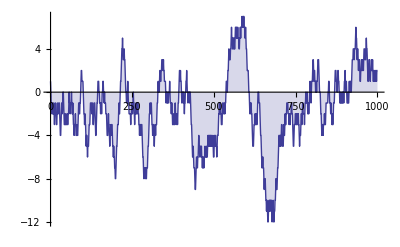

```mathematica
DiscretePlot[ DDa[n,-1],{n,1,1000}]
```

```mathematica
(1+1/List@@NRoots[ DDa[221,x]==0,x][[All,2]])
```

{0.968083,0.929078+0.0404926 ⅈ,0.929078-0.0404926 ⅈ,0.734395+0.230064 ⅈ,0.734395-0.230064 ⅈ,-0.205371,-49.0992}

```mathematica
(List@@NRoots[ DDa[221,x]==0,x][[All,2]])
```

{-31.331,-10.6336-6.07118 ⅈ,-10.6336+6.07118 ⅈ,-2.15108-1.86324 ⅈ,-2.15108+1.86324 ⅈ,-0.82962,-0.0199604}

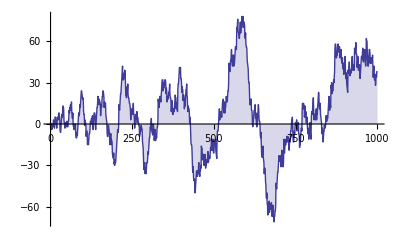

```mathematica
DiscretePlot[ DDa[n,-2],{n,1,1000}]
```

```mathematica
(1-1/List@@NRoots[ DDa[221,x]==0,x][[All,2]])
```

{1.03192,1.07092-0.0404926 ⅈ,1.07092+0.0404926 ⅈ,1.2656-0.230064 ⅈ,1.2656+0.230064 ⅈ,2.20537,51.0992}

```mathematica
(List@@NRoots[ DDa[117337,x]==0,x][[All,2]])
```

{-538.728,-31.0949-83.461 ⅈ,-31.0949+83.461 ⅈ,-15.7211,-13.4864-22.1035 ⅈ,-13.4864+22.1035 ⅈ,-7.97607-11.9414 ⅈ,-7.97607+11.9414 ⅈ,-3.61902-5.17153 ⅈ,-3.61902+5.17153 ⅈ,-2.58457-2.27341 ⅈ,-2.58457+2.27341 ⅈ,-1.65895-0.738425 ⅈ,-1.65895+0.738425 ⅈ,-0.946108,-0.0000899707}

```mathematica
(-1/List@@NRoots[ DDa[117337,x]==0,x][[All,2]])
```

{0.00185622,0.00391987-0.0105212 ⅈ,0.00391987+0.0105212 ⅈ,0.0636086,0.0201155-0.0329682 ⅈ,0.0201155+0.0329682 ⅈ,0.0386785-0.0579076 ⅈ,0.0386785+0.0579076 ⅈ,0.0908342-0.129801 ⅈ,0.0908342+0.129801 ⅈ,0.218137-0.191875 ⅈ,0.218137+0.191875 ⅈ,0.503111-0.223943 ⅈ,0.503111+0.223943 ⅈ,1.05696,11114.7}

```mathematica
(1-1/List@@NRoots[ DDa[117337,x]==0,x][[All,2]])
```

{1.00186,1.00392-0.0105212 ⅈ,1.00392+0.0105212 ⅈ,1.06361,1.02012-0.0329682 ⅈ,1.02012+0.0329682 ⅈ,1.03868-0.0579076 ⅈ,1.03868+0.0579076 ⅈ,1.09083-0.129801 ⅈ,1.09083+0.129801 ⅈ,1.21814-0.191875 ⅈ,1.21814+0.191875 ⅈ,1.50311-0.223943 ⅈ,1.50311+0.223943 ⅈ,2.05696,11115.7}

```mathematica
(1+1/List@@NRoots[ DDa[117337,x]==0,x][[All,2]])
```

{0.998144,0.99608+0.0105212 ⅈ,0.99608-0.0105212 ⅈ,0.936391,0.979884+0.0329682 ⅈ,0.979884-0.0329682 ⅈ,0.961322+0.0579076 ⅈ,0.961322-0.0579076 ⅈ,0.909166+0.129801 ⅈ,0.909166-0.129801 ⅈ,0.781863+0.191875 ⅈ,0.781863-0.191875 ⅈ,0.496889+0.223943 ⅈ,0.496889-0.223943 ⅈ,-0.0569616,-11113.7}

```mathematica
(1-2/List@@NRoots[ DDa[117337,x]==0,x][[All,2]])
```

{1.00371,1.00784-0.0210424 ⅈ,1.00784+0.0210424 ⅈ,1.12722,1.04023-0.0659365 ⅈ,1.04023+0.0659365 ⅈ,1.07736-0.115815 ⅈ,1.07736+0.115815 ⅈ,1.18167-0.259602 ⅈ,1.18167+0.259602 ⅈ,1.43627-0.38375 ⅈ,1.43627+0.38375 ⅈ,2.00622-0.447885 ⅈ,2.00622+0.447885 ⅈ,3.11392,22230.5}

```mathematica
(1+1/List@@NRoots[ DDD[530617337,x]==0,x][[All,2]])
```

{0.999687,0.998591,0.987255,0.998376+0.00544341 ⅈ,0.998376-0.00544341 ⅈ,0.998094+0.00809593 ⅈ,0.998094-0.00809593 ⅈ,0.985423+0.0236715 ⅈ,0.985423-0.0236715 ⅈ,0.942226+0.0475071 ⅈ,0.942226-0.0475071 ⅈ,0.993499+0.0260563 ⅈ,0.993499-0.0260563 ⅈ,0.883949,0.979123+0.0508231 ⅈ,0.979123-0.0508231 ⅈ,0.955838+0.0802674 ⅈ,0.955838-0.0802674 ⅈ,0.90885+0.121061 ⅈ,0.90885-0.121061 ⅈ,0.829949+0.144261 ⅈ,0.829949-0.144261 ⅈ,0.722644+0.159157 ⅈ,0.722644-0.159157 ⅈ,0.508028+0.103477 ⅈ,0.508028-0.103477 ⅈ,-0.0042037,-2.78828×10^7}

```mathematica
N[lin[ 530617337]]
```

2.78828×10^7

```mathematica
N[LogIntegral[530617337]]
```

2.78831×10^7

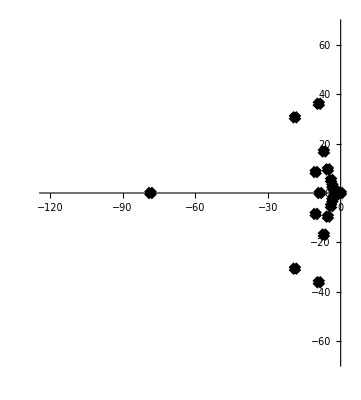

```mathematica
RootLocusPlot[1/Expand[DDD[530617337,x]],{k,0,1},FeedbackType->None]
```

```mathematica
3.036429505056579*^6
```

```mathematica
3.036426152187806*^6
```

3.03643×10^6

```mathematica
3.036368981104197*^6
```

```mathematica
{8.^5,11.^7,13.^9};
NumberForm[2.78828270840755*^7,ExponentFunction->(If[-10<#<10,Null,#]&)]
```

27882827.

```mathematica
NumberForm[2.7882830574696146*^7,ExponentFunction->(If[-10<#<10,Null,#]&)]
```

27882831.

```mathematica
NumberForm[2.7883111397742484*^7,ExponentFunction->(If[-10<#<10,Null,#]&)]
```

27883111.

```mathematica
NumberForm[2.7883111397742484*^7-2.7882830574696146*^7,ExponentFunction->(If[-10<#<10,Null,#]&)]
```

280.823

```mathematica
Floor[Log[2,n]]
```

15

```mathematica
Table[ {n,(lin[n]+1/List@@NRoots[ DDD[n,x]==0,x][[All,2]])[[Floor[Log[2,n]]]]},{n,2312002,2312100}]//TableForm
```

2312002 | 3.13588
2312003 | 3.13588
2312004 | 3.13588
2312005 | 3.13589
2312006 | 3.13589
2312007 | 3.13589
2312008 | 3.13589
2312009 | 3.1359
2312010 | 3.1359
2312011 | 3.1359
2312012 | 3.1359
2312013 | 3.1359
2312014 | 3.1359
2312015 | 3.1359
2312016 | 3.1359
2312017 | 3.1359
2312018 | 3.13591
2312019 | 3.13591
2312020 | 3.13591
2312021 | 3.13589
2312022 | 3.13589
2312023 | 3.13589
2312024 | 3.13589
2312025 | 3.13589
2312026 | 3.1359
2312027 | 3.13588
2312028 | 3.13588
2312029 | 3.13589
2312030 | 3.13589
2312031 | 3.13589
2312032 | 3.13589
2312033 | 3.13589
2312034 | 3.13589
2312035 | 3.13589
2312036 | 3.13589
2312037 | 3.13589
2312038 | 3.13589
2312039 | 3.1359
2312040 | 3.1359
2312041 | 3.13591
2312042 | 3.13591
2312043 | 3.13591
2312044 | 3.13591
2312045 | 3.13591
2312046 | 3.13591
2312047 | 3.13592
2312048 | 3.13592
2312049 | 3.13592
2312050 | 3.13592
2312051 | 3.13592
2312052 | 3.13592
2312053 | 3.13592
2312054 | 3.13592
2312055 | 3.13592
2312056 | 3.13592
2312057 | 3.13593
2312058 | 3.13593
2312059 | 3.13594
2312060 | 3.13594
2312061 | 3.13594
2312062 | 3.13594
2312063 | 3.13594
2312064 | 3.13594
2312065 | 3.13594
2312066 | 3.13595
2312067 | 3.13595
2312068 | 3.13595
2312069 | 3.13593
2312070 | 3.13593
2312071 | 3.13593
2312072 | 3.13593
2312073 | 3.13593
2312074 | 3.13594
2312075 | 3.13594
2312076 | 3.13594
2312077 | 3.13595
2312078 | 3.13595
2312079 | 3.13595
2312080 | 3.13595
2312081 | 3.13596
2312082 | 3.13596
2312083 | 3.13596
2312084 | 3.13596
2312085 | 3.13596
2312086 | 3.13596
2312087 | 3.13597
2312088 | 3.13597
2312089 | 3.13597
2312090 | 3.13597
2312091 | 3.13597
2312092 | 3.13597
2312093 | 3.13597
2312094 | 3.13597
2312095 | 3.13598
2312096 | 3.13598
2312097 | 3.13598
2312098 | 3.13598
2312099 | 3.13596
2312100 | 3.13596

```mathematica
Table[ {n,(1+1/List@@NRoots[ DDD[n,x]==0,x][[All,2]])[[Floor[Log[2,n]]-1]]},{n,3000, 3100}]//TableForm
```

3000 | 0.0963284
3001 | 0.118497
3002 | 0.161083
3003 | 0.114568
3004 | 0.116244
3005 | 0.0928747
3006 | 0.0917045
3007 | 0.0724982
3008 | 0.0725378
3009 | 0.0939202
3010 | 0.0710646
3011 | 0.0878256
3012 | 0.086834
3013 | 0.069179
3014 | 0.0886674
3015 | 0.0876493
3016 | 0.0873493
3017 | 0.0695501
3018 | 0.0892121
3019 | 0.107974
3020 | 0.106502
3021 | 0.134576
3022 | 0.109173
3023 | 0.130868
3024 | 0.130874
3025 | 0.130722
3026 | 0.171764
3027 | 0.135018
3028 | 0.137378
3029 | 0.110826
3030 | 0.0856058
3031 | 0.068332
3032 | 0.0685182
3033 | 0.0691302
3034 | 0.0885638
3035 | 0.0703974
3036 | 0.0711599
3037 | 0.087985
3038 | 0.0869866
3039 | 0.0692658
3040 | 0.0692076
3041 | 0.0853113
3042 | 0.0853548
3043 | 0.0680959
3044 | 0.0687005
3045 | 0.051215
3046 | 0.0372398
3047 | 0.0241409
3048 | 0.0240886
3049 | 0.0366599
3050 | 0.0364002
3051 | 0.03648
3052 | 0.0362232
3053 | 0.0235276
3054 | 0.0367217
3055 | 0.0512062
3056 | 0.0512662
3057 | 0.0372769
3058 | 0.0520638
3059 | 0.0686811
3060 | 0.0686552
3061 | 0.084539
3062 | 0.067543
3063 | 0.0520937
3064 | 0.0522223
3065 | 0.0379105
3066 | 0.0239017
3067 | 0.0363533
3068 | 0.0360985
3069 | 0.0358479
3070 | 0.0498555
3071 | 0.0363346
3072 | 0.0363396
3073 | 0.0236011
3074 | 0.0368415
3075 | 0.036579
3076 | 0.0368317
3077 | 0.023901
3078 | 0.0238757
3079 | 0.0363079
3080 | 0.0363933
3081 | 0.0506984
3082 | 0.0666419
3083 | 0.0818201
3084 | 0.0810059
3085 | 0.0650322
3086 | 0.0503382
3087 | 0.0503351
3088 | 0.0503928
3089 | 0.0641275
3090 | 0.0482474
3091 | 0.0352409
3092 | 0.0354734
3093 | 0.0230716
3094 | 0.0110171
3095 | 4.44089×10^-16
3096 | 2.22045×10^-16
3097 | -0.0105989
3098 | -0.0208262
3099 | -0.0307204
3100 | -0.0307183

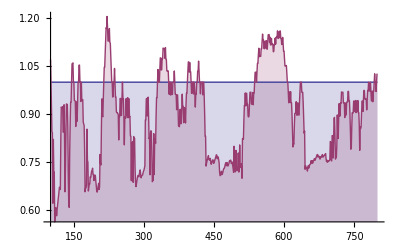

```mathematica
DiscretePlot[{1, Re[(-1/List@@NRoots[ DDD[n,x]==0,x][[All,2]])[[Floor[Log[2,n]]-1]]]},{n,100,800}]//TableForm
```

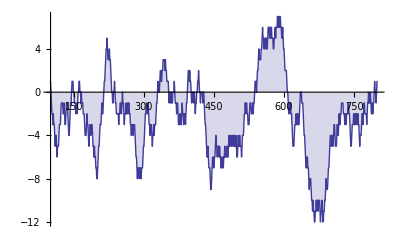

```mathematica
DiscretePlot[ DDD[n,-1],{n,100,800}]
```

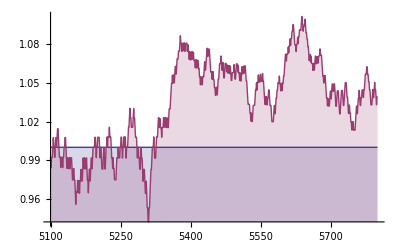

```mathematica
DiscretePlot[{1, Re[(-1/List@@NRoots[ DDD[n,x]==0,x][[All,2]])[[Floor[Log[2,n]]-1]]]},{n,5100,5800}]//TableForm
```

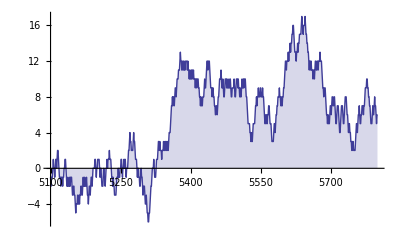

```mathematica
DiscretePlot[ DDD[n,-1],{n,5100,5800}]
```

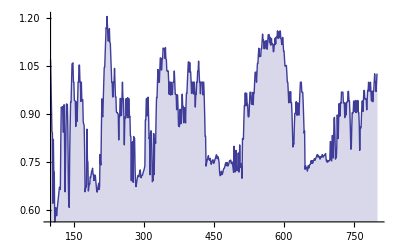

```mathematica
DiscretePlot[{ Re[(-1/List@@NRoots[ DDD[n,x]==0,x][[All,2]])[[Floor[Log[2,n]]-1]]]},{n,100,800}]//TableForm
```

```mathematica
RootLocusPlot[1/Expand[DDD[43530617337,x]],{k,0,1},FeedbackType->None]
```

$Aborted

```mathematica
(-1/List@@NRoots[ (DDa[100,x])==0,x][[All,2]])
```

{0.0401208-0.0444144 ⅈ,0.0401208+0.0444144 ⅈ,0.251933-0.17555 ⅈ,0.251933+0.17555 ⅈ,1.07088,26.8783}

```mathematica
(-1/List@@NRoots[ (DDa[100,x]-1)==0,x][[All,2]])
```

Power::infy: Infinite expression 1/0. encountered.

{0.0401206-0.0444142 ⅈ,0.0401206+0.0444142 ⅈ,0.252763-0.176711 ⅈ,0.252763+0.176711 ⅈ,1.,ComplexInfinity}

```mathematica
(-1/List@@NRoots[ (DDa[100,x]-1)/x==0,x][[All,2]])
```

{0.0401206-0.0444142 ⅈ,0.0401206+0.0444142 ⅈ,0.252763-0.176711 ⅈ,0.252763+0.176711 ⅈ,1.}

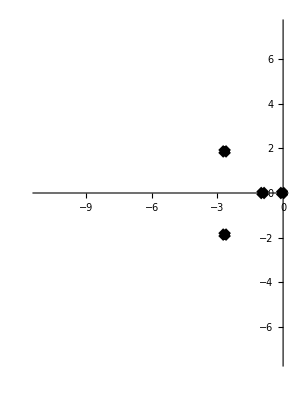

```mathematica
RootLocusPlot[1/Expand[DDa[100,x]],{k,0,1},FeedbackType->None]
```

```mathematica
(List@@NRoots[ (DDa[100,x])==0,x][[All,2]])
```

{-11.1997-12.3982 ⅈ,-11.1997+12.3982 ⅈ,-2.67195-1.86184 ⅈ,-2.67195+1.86184 ⅈ,-0.933809,-0.0372047}

```mathematica
(List@@NRoots[ ((DDD[100000,x]-1)/x)==0,x][[All,2]])
```

```mathematica
rr1:={-56.64116605832289-181.11603126185645 ⅈ,-56.64116605832289+181.11603126185645 ⅈ,-36.31942565534795,-21.11288550721666-38.849319644086606 ⅈ,-21.11288550721666+38.849319644086606 ⅈ,-9.764286440884442-14.385380039003522 ⅈ,-9.764286440884442+14.385380039003522 ⅈ,-4.797724164350477-7.268617575567637 ⅈ,-4.797724164350477+7.268617575567637 ⅈ,-3.0884655016248503-3.388391127081218 ⅈ,-3.0884655016248503+3.388391127081218 ⅈ,-2.1224553042937124-1.3260130474564402 ⅈ,-2.1224553042937124+1.3260130474564402 ⅈ,-1.448195969849161,-1.0607653625930609}
```

```mathematica
(List@@NRoots[ ((DDD[100000,x]))==0,x][[All,2]])
```

```mathematica
rr2:={-56.641166058322895-181.11603126185645 ⅈ,-56.641166058322895+181.11603126185645 ⅈ,-36.31942565534757,-21.11288550721674-38.84931964408693 ⅈ,-21.11288550721674+38.84931964408693 ⅈ,-9.76428644069197-14.385380039419529 ⅈ,-9.76428644069197+14.385380039419529 ⅈ,-4.797724032615504-7.268617517399808 ⅈ,-4.797724032615504+7.268617517399808 ⅈ,-3.08847538375192-3.38838962034819 ⅈ,-3.08847538375192+3.38838962034819 ⅈ,-2.1222879433588195-1.3261002367389711 ⅈ,-2.1222879433588195+1.3261002367389711 ⅈ,-1.449858582932226,-1.059314138745821,-0.00010383223512402999}
```

```mathematica
(List@@NRoots[ ((DDD[100000,x]-1)/x)==0,x][[All,2]]-List@@NRoots[ ((DDD[100000,x]))==0,x][[All,2]])
```

Thread::tdlen: Objects of unequal length in {-56.6412 - 181.116\ ⅈ, -56.6412 + 181.116\ ⅈ, -36.3194, -21.1129 - 38.8493\ ⅈ, -21.1129 + 38.8493\ ⅈ, -9.76429 - 14.3854\ ⅈ, « 3 », -3.08847 - 3.38839\ ⅈ, -3.08847 + 3.38839\ ⅈ, -2.12246 - 1.32601\ ⅈ, -2.12246 + 1.32601\ ⅈ, -1.4482, -1.06077} + {« 1 »} cannot be combined.

```mathematica
99999 Product[ 1+1/(j-1),{j,rr1}]
```

9633.77+1.73471×10^-13 ⅈ

```mathematica
N[Sum[ MangoldtLambda[j]/Log[j],{j,2,100000}]]
```

9633.77

```mathematica
(1+1/(-1+List@@NRoots[ ((DDD[100000,x]-1)/x)==0,x][[All,2]]))
```

{0.998404+0.00501352 ⅈ,0.998404-0.00501352 ⅈ,0.973204,0.988934+0.0194417 ⅈ,0.988934-0.0194417 ⅈ,0.966654+0.0445631 ⅈ,0.966654-0.0445631 ⅈ,0.932933+0.0840824 ⅈ,0.932933-0.0840824 ⅈ,0.855002+0.12017 ⅈ,0.855002-0.12017 ⅈ,0.728672+0.115225 ⅈ,0.728672-0.115225 ⅈ,0.591536,0.514743}

```mathematica
N[Sum[MoebiusMu[j],{j,2,100000}]]
```

-49.

```mathematica
99999 Product[ 1+2/(j-1),{j,rr1}]
```

49.-1.35524×10^-15 ⅈ

```mathematica
(1+2/(-1+List@@NRoots[ ((DDD[100000,x]-1)/x)==0,x][[All,2]]))
```

{0.996809+0.010027 ⅈ,0.996809-0.010027 ⅈ,0.946409,0.977868+0.0388834 ⅈ,0.977868-0.0388834 ⅈ,0.933309+0.0891263 ⅈ,0.933309-0.0891263 ⅈ,0.865865+0.168165 ⅈ,0.865865-0.168165 ⅈ,0.710004+0.240339 ⅈ,0.710004-0.240339 ⅈ,0.457344+0.23045 ⅈ,0.457344-0.23045 ⅈ,0.183072,0.0294868}

```mathematica
(100000^.5)/100000
```

0.00316228

```mathematica
Product[ 1+2/(j-1),{j,rr1}]
```

0.000490005-1.35525×10^-20 ⅈ

```mathematica
(1-1/(-1+List@@NRoots[ ((DDD[100000,x]-1)/x)==0,x][[All,2]]))
```

{1.0016-0.00501352 ⅈ,1.0016+0.00501352 ⅈ,1.0268,1.01107-0.0194417 ⅈ,1.01107+0.0194417 ⅈ,1.03335-0.0445631 ⅈ,1.03335+0.0445631 ⅈ,1.06707-0.0840824 ⅈ,1.06707+0.0840824 ⅈ,1.145-0.12017 ⅈ,1.145+0.12017 ⅈ,1.27133-0.115225 ⅈ,1.27133+0.115225 ⅈ,1.40846,1.48526}

```mathematica
ff[n_, z_] :=ff[n,z]=Re[(1-(z-1)/(-1+List@@NRoots[ ((DDD[n,x]-1)/x)==0,x][[All,2]]))]
```

```mathematica
ff[100000,-1]
```

{0.996809+0.010027 ⅈ,0.996809-0.010027 ⅈ,0.946409,0.977868+0.0388834 ⅈ,0.977868-0.0388834 ⅈ,0.933309+0.0891263 ⅈ,0.933309-0.0891263 ⅈ,0.865865+0.168165 ⅈ,0.865865-0.168165 ⅈ,0.710004+0.240339 ⅈ,0.710004-0.240339 ⅈ,0.457344+0.23045 ⅈ,0.457344-0.23045 ⅈ,0.183072,0.0294868}

```mathematica
DiscretePlot[ {Product[ v, {v,ff[n,-1]}],Product[ v, {v,ff[n,0]}],Product[ v, {v,ff[n,2]}]},{n,10,7000,10}]
```

-Graphics-

```mathematica
(1+2/(-1+List@@NRoots[ ((DDD[1000000,x]-1)/x)==0,x][[All,2]]))
```

{0.998234,0.983374,0.988687+0.02016 ⅈ,0.988687-0.02016 ⅈ,0.979719+0.0490487 ⅈ,0.979719-0.0490487 ⅈ,0.926156+0.0759418 ⅈ,0.926156-0.0759418 ⅈ,0.913899+0.141541 ⅈ,0.913899-0.141541 ⅈ,0.643831,0.783419+0.210792 ⅈ,0.783419-0.210792 ⅈ,0.600412+0.215079 ⅈ,0.600412-0.215079 ⅈ,0.332513+0.14334 ⅈ,0.332513-0.14334 ⅈ,-0.0136864}

```mathematica
DiscretePlot[ ff[n,-1][[Length[ff[n,-1]]]],{n,100,5000}]
```

-Graphics-

```mathematica
ff[1000000,-1][[Length[ff[1000000,-1]]]]
```

-0.0136864

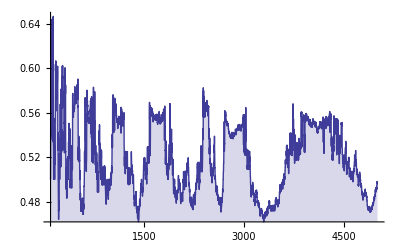

```mathematica
DiscretePlot[ ff[n,0][[Length[ff[n,0]]]],{n,100,5000}]
```

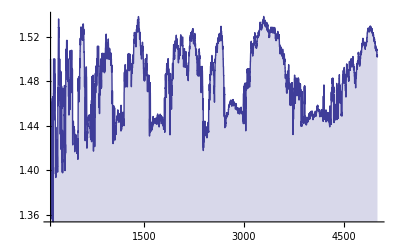

```mathematica
DiscretePlot[ ff[n,2][[Length[ff[n,2]]]],{n,100,5000}]
```

```mathematica
Expand[(a+b I)(a-b I)]
```

a^2+b^2

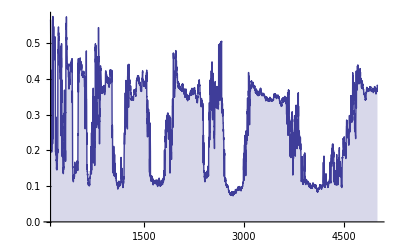

```mathematica
DiscretePlot[ ff[n,-1][[-1+Length[ff[n,-1]]]],{n,100,5000}]
```

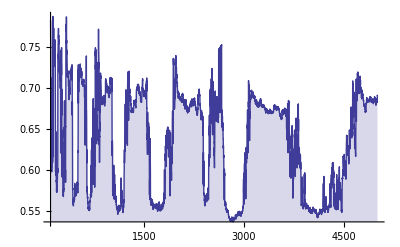

```mathematica
DiscretePlot[ ff[n,0][[-1+Length[ff[n,0]]]],{n,100,5000}]
```

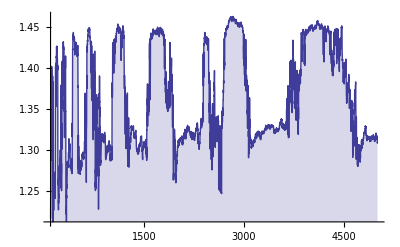

```mathematica
DiscretePlot[ ff[n,2][[-1+Length[ff[n,2]]]],{n,100,5000}]
```

```mathematica
(1+2/(-1+List@@NRoots[ ((DDD[100000,x]-1)/x)==0,x][[All,2]]))
```

{0.996809+0.010027 ⅈ,0.996809-0.010027 ⅈ,0.946409,0.977868+0.0388834 ⅈ,0.977868-0.0388834 ⅈ,0.933309+0.0891263 ⅈ,0.933309-0.0891263 ⅈ,0.865865+0.168165 ⅈ,0.865865-0.168165 ⅈ,0.710004+0.240339 ⅈ,0.710004-0.240339 ⅈ,0.457344+0.23045 ⅈ,0.457344-0.23045 ⅈ,0.183072,0.0294868}

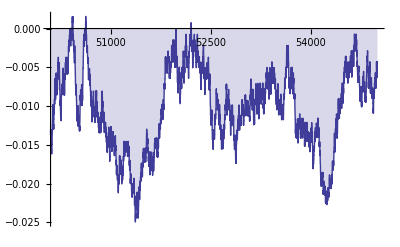

```mathematica
DiscretePlot[ ff[n,-1][[Length[ff[n,-1]]]],{n,50100,55000}]
```

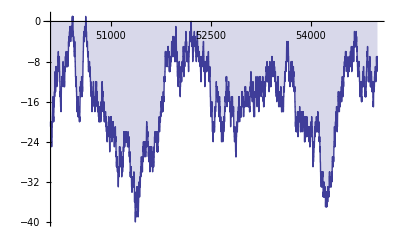

```mathematica
DiscretePlot[ -DDD[n,-1],{n,50100,55000}]
```

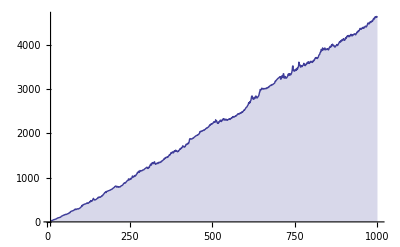

```mathematica
DiscretePlot[ 1+2(n-1)Product[ ff[n,2][[j]],{j,1,-1+Length[ff[n,-1]]}],{n,10,1000}]
```

```mathematica
(1+2/(-1+List@@NRoots[ ((DDD[480,x]-1)/x)==0,x][[All,2]]))
```

{0.981292,0.905037+0.121114 ⅈ,0.905037-0.121114 ⅈ,0.644195+0.229302 ⅈ,0.644195-0.229302 ⅈ,0.143483+0.132718 ⅈ,0.143483-0.132718 ⅈ}